```mathematica
Clear["Global`*"]
```

### Definitions:

```mathematica
logsim:={a_ Log[x_]-a_ Log[ z_]->a*Log[x/z]};
Shafersineq:={ArcTan[x_]->(3x)/(1+2Sqrt[1+x^2])};
logineqgeq:={Log[1+x_]->x,Log[1+x_]->x/Sqrt[1+x]};
logineqleq:={Log[1+x_]-> x/(1-x),Log[1+x_]->(2x)/(2-x)};
int1[y_,α_,x_,a_]:=2Pi((Integrate[q^2/(q^2+#1*y*q+α),q])/.q->x&@@{a})
```

```mathematica
int1[y,α,x,a];
```

```mathematica
intq[R_,y_,α_,a_]:=(int1[y,α,R,#])-(int1[y,α,0,#])&@@{a}//Simplify
```

```mathematica
int2[R_,y_,α_,a_]:=Evaluate[Integrate[intq[R,y,α,q1],q1]]/.q1->a
```

```mathematica
int2[R,y,α,1]-int2[R,y,α,-1]//Simplify//Expand;
```

```mathematica
intqθ[R_,y_,α_]:=(int2[#1,#2,#3,1])-(int2[#1,#2,#3,-1])&@@{R,y,α}//Simplify//Expand
ll[x1_,x2_,x3_]:=ll[x1,x2,x3]=Evaluate[4Pi*x1-Evaluate[intqθ[#1,#2,#3]&@@{x1,x2,x3}]//Simplify];
```

```mathematica
intqθ[R,y,α];
```

```mathematica
ll[x1,x2,x3]//FullSimplify;
```

```mathematica
L[R_,y_,α_]:=L[R,y,α]=ll[x1,x2,x3]/.{x1->R,x2->y,x3->α}
```

```mathematica
int21[y_,α_,x_,a_]:=2Pi((Integrate[q^4/((q^2+#1*y*q+α)^2),q])/.q->x&@@{a})
```

```mathematica
int21[y,α,x,a];
```

```mathematica
int2q[R_,y_,α_,a_]:=(int21[y,α,R,#])-(int21[y,α,0,#])&@@{a}//Simplify
```

```mathematica
int22[R_,y_,α_,a_]:=Evaluate[Integrate[int2q[R,y,α,q1],q1]]/.q1->a
```

```mathematica
int22[R,y,α,1]-int22[R,y,α,-1]//Simplify//Expand;
```

```mathematica
int2qθ[R_,y_,α_]:=(int22[#1,#2,#3,1])-(int22[#1,#2,#3,-1])&@@{R,y,α}//Simplify//Expand
ll2[x1_,x2_,x3_]:=ll2[x1,x2,x3]=Evaluate[4Pi*x1-Evaluate[int2qθ[#1,#2,#3]&@@{x1,x2,x3}]//Simplify];
```

```mathematica
int2qθ[R,y,α];
```

```mathematica
ll2[x1,x2,x3]//FullSimplify;
```

```mathematica
L2[R_,y_,α_]:=L2[R,y,α]=ll2[x1,x2,x3]/.{x1->R,x2->y,x3->α}
```

```mathematica
L2[R,y,α]
```

(π (2 y (y^2-3 α) √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y (y^2-3 α) √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]-(y^4-5 y^2 α+4 α^2) (Log[R^2-R y+α]-Log[R^2+R y+α])))/(y^3-4 y α)

```mathematica
L[R,y,α]
```

(π (4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α]))/(2 y)

### Expression for L^R

```mathematica
L[R,2/(m+1)R,R^2+μ]//FullSimplify
```

1/2 π (4 R+4 √((m (2+m) R^2)/(1+m)^2+μ) (ArcTan[(m R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))]+ArcTan[((2+m) R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))])+((μ+m (2+m) (2 R^2+μ)) (Log[(2 m R^2)/(1+m)+μ]-Log[(2 (2+m) R^2)/(1+m)+μ]))/((1+m) R))

(π (-((1+m) (-2+(2 m (2+m))/(2+2 m+m^2)) √μ)/(√(2+m))+1/2 π √((2+m) μ)+2 √((2+m) μ) ArcTan[m/(2+m)]))/(√2)

### L^R has maximum in R only when k<=1+1/3, where k=α/(y^2/4).

```mathematica
Manipulate[Manipulate[Plot[{L[R,y,k*y^2/4]},{R,0,100}],{k,1.001,3}],{y,1,100}]
```

```mathematica
D[L[R,y,k*y^2/4],R]
```

(π (4 y+(2 R^2 (2 R-y))/(R^2-R y+(k y^2)/4)-((2 R-y) y^2)/(R^2-R y+(k y^2)/4)+(k (2 R-y) y^2)/(2 (R^2-R y+(k y^2)/4))-(2 R^2 (2 R+y))/(R^2+R y+(k y^2)/4)+(y^2 (2 R+y))/(R^2+R y+(k y^2)/4)-(k y^2 (2 R+y))/(2 (R^2+R y+(k y^2)/4))+(4 y)/(1+(2 R-y)^2/(-y^2+k y^2))+(4 y)/(1+(2 R+y)^2/(-y^2+k y^2))+4 R Log[R^2-R y+(k y^2)/4]-4 R Log[R^2+R y+(k y^2)/4]))/(2 y)

```mathematica
dL[R_,y_,α_]=Evaluate[D[L[R,y,α],R]]
```

(π (4 y+(2 R^2 (2 R-y))/(R^2-R y+α)-((2 R-y) y^2)/(R^2-R y+α)+(2 (2 R-y) α)/(R^2-R y+α)-(2 R^2 (2 R+y))/(R^2+R y+α)+(y^2 (2 R+y))/(R^2+R y+α)-(2 (2 R+y) α)/(R^2+R y+α)+(4 y)/(1+(2 R-y)^2/(-y^2+4 α))+(4 y)/(1+(2 R+y)^2/(-y^2+4 α))+4 R Log[R^2-R y+α]-4 R Log[R^2+R y+α]))/(2 y)

```mathematica
Manipulate[Manipulate[Manipulate[Manipulate[Plot[{(4Pi-dL[R,y,k*y^2/4+μ])/(4Pi*R+α)-(L[R,y,k*y^2/4+μ]*4Pi)/(4Pi*R+α)^2},{R,11,10000}],{k,1.001,3}],{y,1,1000}],{α,-10,10}],{μ,0,1000}]
```

```mathematica
Manipulate[Manipulate[Plot[{L[R,y,k*y^2/4]},{R,0,100}],{k,1.001,3}],{y,1,100}]
```

```mathematica
%//Simplify
```

(2 π (2 y+R Log[4 R^2-4 R y+k y^2]-R Log[4 R^2+4 R y+k y^2]))/y

```mathematica
g[R_,y_,α_]:=(2 y+R Log[R^2-R y+α]-R Log[R (R+y)+α])/y;
```

```mathematica
Manipulate[Manipulate[Plot[g[R,y,k*y^2/4],{R,1,1000}],{k,1.001,3}],{y,1,10}]
```

### Inequalities between different part of L^R

```mathematica
L[R,y,k*y^2/4]//FullSimplify
```

2 π R+√(-1+k) π y ArcTan[(2 R-y)/(√(-1+k) y)]+√(-1+k) π y ArcTan[(2 R+y)/(√(-1+k) y)]+(π (4 R^2+(-2+k) y^2) (Log[4 R^2-4 R y+k y^2]-Log[4 R^2+4 R y+k y^2]))/(4 y)

```mathematica
(2/y L[y/2,y,k*y^2/4]//FullSimplify)//.logsim
```

1/2 π (4+4 √(-1+k) ArcTan[2/(√(-1+k))]+(-1+k) Log[(-1+k)/(3+k)])

```mathematica
%/.logsim
```

1/2 π (4+4 √(-1+k) ArcTan[2/(√(-1+k))]+(-1+k) Log[(-1+k)/(3+k)])

```mathematica
Manipulate[Manipulate[Plot[{2Pi(4 √(-1+k) y ArcTan[(2 R-y)/(√(-1+k) y)]+4 √(-1+k) y ArcTan[(2 R+y)/(√(-1+k) y)]),2Pi(16/(1+1/(-1+k))R),8Pi*R,8L[R,y,k*y^2/4],8*1/2 π (4+4 √(-1+k) ArcTan[2/(√(-1+k))]+(-1+k) Log[(-1+k)/(3+k)])*R,8*4Pi*R},{R,0,y/2}],{k,1.34,3}],{y,10,10000}]
```

```mathematica
L[R,2/(m+1)R,R^2+μ]//Simplify
```

1/(4 R)(1+m) π ((8 R^2)/(1+m)+(8 R √((μ+2 m (R^2+μ)+m^2 (R^2+μ))/(1+m)^2) ArcTan[(m R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))])/(1+m)+(8 R √((μ+2 m (R^2+μ)+m^2 (R^2+μ))/(1+m)^2) ArcTan[((2+m) R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))])/(1+m)-4 R^2 Log[(2 (2+m) R^2)/(1+m)+μ]+(4 R^2 Log[(2 (2+m) R^2)/(1+m)+μ])/(1+m)^2-2 μ Log[(2 (2+m) R^2)/(1+m)+μ]+4 R^2 Log[(2 m R^2+μ+m μ)/(1+m)]-(4 R^2 Log[(2 m R^2+μ+m μ)/(1+m)])/(1+m)^2+2 μ Log[(2 m R^2+μ+m μ)/(1+m)])

```mathematica
%//FullSimplify
```

1/2 π (4 R+4 √((m (2+m) R^2)/(1+m)^2+μ) (ArcTan[(m R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))]+ArcTan[((2+m) R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))])+((μ+m (2+m) (2 R^2+μ)) (Log[(2 m R^2)/(1+m)+μ]-Log[(2 (2+m) R^2)/(1+m)+μ]))/((1+m) R))

```mathematica
%221/.{ArcTan[x_]->(3x)/(1+2Sqrt[1+x^2])}
```

1/2 π (4 R+4 √((m (2+m) R^2)/(1+m)^2+μ) ((3 m R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ) (1+2 √(1+(m^2 R^2)/((1+m)^2 ((m (2+m) R^2)/(1+m)^2+μ)))))+(3 (2+m) R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ) (1+2 √(1+((2+m)^2 R^2)/((1+m)^2 ((m (2+m) R^2)/(1+m)^2+μ))))))+((μ+m (2+m) (2 R^2+μ)) (Log[(2 m R^2)/(1+m)+μ]-Log[(2 (2+m) R^2)/(1+m)+μ]))/((1+m) R))

```mathematica
%/.Log[a_]-Log[b_]->Log[a/b]
```

1/2 π (4 R+4 √((m (2+m) R^2)/(1+m)^2+μ) ((3 m R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ) (1+2 √(1+(m^2 R^2)/((1+m)^2 ((m (2+m) R^2)/(1+m)^2+μ)))))+(3 (2+m) R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ) (1+2 √(1+((2+m)^2 R^2)/((1+m)^2 ((m (2+m) R^2)/(1+m)^2+μ))))))+((μ+m (2+m) (2 R^2+μ)) Log[((2 m R^2)/(1+m)+μ)/((2 (2+m) R^2)/(1+m)+μ)])/((1+m) R))

```mathematica
%//Simplify
```

1/2 π (4 R+(12 m R)/((1+m) (1+2 √(1+(m^2 R^2)/(μ+2 m (R^2+μ)+m^2 (R^2+μ)))))+(12 (2+m) R)/((1+m) (1+2 √(1+((2+m)^2 R^2)/(μ+2 m (R^2+μ)+m^2 (R^2+μ)))))+(μ Log[(2 m R^2+μ+m μ)/(4 R^2+2 m R^2+μ+m μ)])/(R+m R)+(m (2+m) (2 R^2+μ) Log[(μ+m (2 R^2+μ))/(2 (2+m) R^2+(1+m) μ)])/((1+m) R))

```mathematica
%//FullSimplify
```

1/2 π (4 R (1+(3 (1/(1/2+√(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+m (1/(1+2 √(((1+m) (2 m R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+1/(1+2 √(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ)))))))/(1+m))+((μ+m (2+m) (2 R^2+μ)) Log[1-(4 R^2)/(2 (2+m) R^2+μ+m μ)])/((1+m) R))

```mathematica
%/.{Log[1-x_]->(-1/x)/Sqrt[1+1/x]}
```

```mathematica
1/2 π (4 R (1+(3 (1/(1/2+√(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+m (1/(1+2 √(((1+m) (2 m R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+1/(1+2 √(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ)))))))/(1+m))-((μ+m (2+m) (2 R^2+μ)) Log[1+(4 R^2)/(2 m R^2+μ+m μ)])/((1+m) R))/.{Log[1+(4 R^2)/(2 m R^2+μ+m μ)]->((4 R^2)/(2 m R^2+μ+m μ))/Sqrt[1+(4 R^2)/(2 m R^2+μ+m μ)]}
```

1/2 π (-(4 R (μ+m (2+m) (2 R^2+μ)))/((1+m) (2 m R^2+μ+m μ) √(1+(4 R^2)/(2 m R^2+μ+m μ)))+4 R (1+(3 (1/(1/2+√(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+m (1/(1+2 √(((1+m) (2 m R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+1/(1+2 √(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ)))))))/(1+m)))

```mathematica
%//FullSimplify
```

2 π R (1-(μ+m (2+m) (2 R^2+μ))/((1+m) (μ+m (2 R^2+μ)) √(1+(4 R^2)/(2 m R^2+μ+m μ)))+(3 (1/(1/2+√(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+m (1/(1+2 √(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+1/(1+2 √(((1+m) (μ+m (2 R^2+μ)))/(μ+m (2+m) (R^2+μ)))))))/(1+m))

```mathematica
1+(4 R^2)/(2 m R^2+μ+m μ)//Expand
```

1-(4 R^2)/(2 (2+m) R^2+μ+m μ)

```mathematica
D[(μ+m (2+m) (2 R^2+μ))/((1+m) (μ+m (2 R^2+μ)) √(1+(4 R^2)/(2 m R^2+μ+m μ))),R]
```

-((μ+m (2+m) (2 R^2+μ)) (-(16 m R^3)/((2 m R^2+μ+m μ)^2)+(8 R)/(2 m R^2+μ+m μ)))/(2 (1+m) (μ+m (2 R^2+μ)) (1+(4 R^2)/(2 m R^2+μ+m μ))^(3/2))+(4 m (2+m) R)/((1+m) (μ+m (2 R^2+μ)) √(1+(4 R^2)/(2 m R^2+μ+m μ)))-(4 m R (μ+m (2+m) (2 R^2+μ)))/((1+m) (μ+m (2 R^2+μ))^2 √(1+(4 R^2)/(2 m R^2+μ+m μ)))

```mathematica
%//Simplify
```

-(4 (1+m) R μ^2)/((2 (2+m) R^2+(1+m) μ) (μ+m (2 R^2+μ))^2 √(1+(4 R^2)/(2 m R^2+μ+m μ)))

```mathematica
(μ+m (2+m) (2 R^2+μ))/((1+m) (μ+m (2 R^2+μ)) √(1+(4 R^2)/(2 m R^2+μ+m μ)))/.R->(1+m)Sqrt[μ]
```

(μ+m (2+m) (μ+2 (1+m)^2 μ))/((1+m) (μ+m (μ+2 (1+m)^2 μ)) √(1+(4 (1+m)^2 μ)/(μ+m μ+2 m (1+m)^2 μ)))

```mathematica
%//Simplify
```

```mathematica
((1+4 m+2 m^2) √((5+6 m+2 m^2)/(1+2 m+2 m^2)))/(5+6 m+2 m^2)//FullSimplify
```

((1+2 m (2+m)) √(1+(4 (1+m))/(1+2 m (1+m))))/(5+2 m (3+m))

```mathematica
D[(3 (1/(1/2+√(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+m (1/(1+2 √(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+1/(1+2 √(((1+m) (μ+m (2 R^2+μ)))/(μ+m (2+m) (R^2+μ)))))))/(1+m),R]
```

(3 (-(-(2 m (1+m) (2+m) R (2 (2+m) R^2+μ+m μ))/((μ+m (2+m) (R^2+μ))^2)+(4 (1+m) (2+m) R)/(μ+m (2+m) (R^2+μ)))/(2 √(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))) (1/2+√(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))^2)+m (-(-(2 m (1+m) (2+m) R (2 (2+m) R^2+μ+m μ))/((μ+m (2+m) (R^2+μ))^2)+(4 (1+m) (2+m) R)/(μ+m (2+m) (R^2+μ)))/(√(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))) (1+2 √(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))^2)-((4 m (1+m) R)/(μ+m (2+m) (R^2+μ))-(2 m (1+m) (2+m) R (μ+m (2 R^2+μ)))/((μ+m (2+m) (R^2+μ))^2))/(√(((1+m) (μ+m (2 R^2+μ)))/(μ+m (2+m) (R^2+μ))) (1+2 √(((1+m) (μ+m (2 R^2+μ)))/(μ+m (2+m) (R^2+μ))))^2))))/(1+m)

```mathematica
%//Simplify
```

(6 (1+m) R μ (-(2 (2+m)^2)/(√(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))) (1+2 √(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))^2)+m (-(2+m)^2/(√(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))) (1+2 √(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))^2)-m^2/(√(((1+m) (μ+m (2 R^2+μ)))/(μ+m (2+m) (R^2+μ))) (1+2 √(((1+m) (μ+m (2 R^2+μ)))/(μ+m (2+m) (R^2+μ))))^2))))/((μ+2 m (R^2+μ)+m^2 (R^2+μ))^2)

```mathematica
Limit[(3 (1/(1/2+√(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+m (1/(1+2 √(((1+m) (2 (2+m) R^2+μ+m μ))/(μ+m (2+m) (R^2+μ))))+1/(1+2 √(((1+m) (μ+m (2 R^2+μ)))/(μ+m (2+m) (R^2+μ)))))))/(1+m),R->Infinity]
```

(3 (2/(1+2 √2 √(1+1/m))+m (1/(1+2 √2 √(1+1/m))+1/(1+2 √2 √((1+m)/(2+m))))))/(1+m)

```mathematica
%//Simplify
```

```mathematica
(3 (2/(1+2 √2 √(1+1/m))+m (1/(1+2 √2 √(1+1/m))+1/(1+2 √2 √((1+m)/(2+m))))))/(1+m)//FullSimplify
```

(3 (2/(1+2 √(2+2/m))+m (1/(1+2 √(2+2/m))+1/(1+2 √2 √((1+m)/(2+m))))))/(1+m)

```mathematica
L[R,2/(m+1)k,k^2+μ]/(2Pi^2 √((k^2 m (2+m))/(1+m)^2+μ))//Simplify
```

1/(8 k π √((k^2 m (2+m))/(1+m)^2+μ))(1+m) ((8 k R)/(1+m)+(8 k √((k^2 m (2+m))/(1+m)^2+μ) ArcTan[(-k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/(1+m)+(8 k √((k^2 m (2+m))/(1+m)^2+μ) ArcTan[(k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/(1+m)-(4 k^2 Log[k^2-(2 k R)/(1+m)+R^2+μ])/(1+m)^2+2 R^2 Log[k^2-(2 k R)/(1+m)+R^2+μ]+2 (k^2+μ) Log[k^2-(2 k R)/(1+m)+R^2+μ]+(4 k^2 Log[k^2+(2 k R)/(1+m)+R^2+μ])/(1+m)^2-2 R^2 Log[k^2+(2 k R)/(1+m)+R^2+μ]-2 (k^2+μ) Log[k^2+(2 k R)/(1+m)+R^2+μ])

```mathematica
%//FullSimplify
```

((4 R)/(√((k^2 m (2+m))/(1+m)^2+μ))+4 ArcTan[(-k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))]+4 ArcTan[(k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))]+((k^2 (-1+m (2+m))+(1+m)^2 (R^2+μ)) (Log[k^2-(2 k R)/(1+m)+R^2+μ]-Log[k^2+(2 k R)/(1+m)+R^2+μ]))/(k (1+m) √((k^2 m (2+m))/(1+m)^2+μ)))/(4 π)

```mathematica
%355/.{Log[k^2-(2 k R)/(1+m)+R^2+μ]-Log[k^2+(2 k R)/(1+m)+R^2+μ]->-(8 k^3 m (2+m) R+4 k (1+m)^2 R μ)/((1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))}
```

((4 R)/(√((k^2 m (2+m))/(1+m)^2+μ))-((8 k^3 m (2+m) R+4 k (1+m)^2 R μ) (k^2 (-1+m (2+m))+(1+m)^2 (R^2+μ)))/(k (1+m)^2 √((k^2 m (2+m))/(1+m)^2+μ) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))+4 ArcTan[(-k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))]+4 ArcTan[(k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/(4 π)

```mathematica
%359/.Shafersineq
```

((4 R)/(√((k^2 m (2+m))/(1+m)^2+μ))+(12 (-k+R+m R))/((1+m) √((k^2 m (2+m))/(1+m)^2+μ) (1+2 √(1+(-k+R+m R)^2/((1+m)^2 ((k^2 m (2+m))/(1+m)^2+μ)))))+(12 (k+R+m R))/((1+m) √((k^2 m (2+m))/(1+m)^2+μ) (1+2 √(1+(k+R+m R)^2/((1+m)^2 ((k^2 m (2+m))/(1+m)^2+μ)))))-((8 k^3 m (2+m) R+4 k (1+m)^2 R μ) (k^2 (-1+m (2+m))+(1+m)^2 (R^2+μ)))/(k (1+m)^2 √((k^2 m (2+m))/(1+m)^2+μ) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ)))))/(4 π)

```mathematica
%//Simplify
```

(4 R-((8 k^3 m (2+m) R+4 k (1+m)^2 R μ) (k^2 (-1+m (2+m))+(1+m)^2 (R^2+μ)))/((1+m)^2 (k (1+m)^2 μ (R^2+μ)+k^3 (μ+m (2+m) (2 R^2+μ))))+(12 (-k+R+m R))/((1+m) (1+2 √(1+(-k+R+m R)^2/(k^2 m (2+m)+(1+m)^2 μ))))+(12 (k+R+m R))/((1+m) (1+2 √(1+(k+R+m R)^2/(k^2 m (2+m)+(1+m)^2 μ)))))/(4 π √((k^2 m (2+m))/(1+m)^2+μ))

```mathematica
4 R-((8 k^3 m (2+m) R+4 k (1+m)^2 R μ) (k^2 (-1+m (2+m))+(1+m)^2 (R^2+μ)))/((1+m)^2 (k (1+m)^2 μ (R^2+μ)+k^3 (μ+m (2+m) (2 R^2+μ))))+(12 (-k+R+m R))/((1+m) (1+2 √(1+(-k+R+m R)^2/(k^2 m (2+m)+(1+m)^2 μ))))+(12 (k+R+m R))/((1+m) (1+2 √(1+(k+R+m R)^2/(k^2 m (2+m)+(1+m)^2 μ))))//Simplify
```

4 R-((8 k^3 m (2+m) R+4 k (1+m)^2 R μ) (k^2 (-1+m (2+m))+(1+m)^2 (R^2+μ)))/((1+m)^2 (k (1+m)^2 μ (R^2+μ)+k^3 (μ+m (2+m) (2 R^2+μ))))+(12 (-k+R+m R))/((1+m) (1+2 √(1+(-k+R+m R)^2/(k^2 m (2+m)+(1+m)^2 μ))))+(12 (k+R+m R))/((1+m) (1+2 √(1+(k+R+m R)^2/(k^2 m (2+m)+(1+m)^2 μ))))

```mathematica
%//FullSimplify
```

4 (R-(R (μ+m (2+m) (2 k^2+μ)) (k^2 (-1+m (2+m))+(1+m)^2 (R^2+μ)))/((1+m)^4 μ (R^2+μ)+k^2 (1+m)^2 (μ+m (2+m) (2 R^2+μ)))+(3 (k+R+m R))/((1+m) (1+2 √(1+(k+R+m R)^2/(μ+m (2+m) (k^2+μ)))))+(3 (-k+R+m R))/((1+m) (1+2 √(1+(k-(1+m) R)^2/(μ+m (2+m) (k^2+μ))))))

```mathematica
Limit[%3,m->Infinity]
```

4 (R+(6 R)/(1+2 √((k^2+R^2+μ)/(k^2+μ)))-(R (2 k^2+μ) (k^2+R^2+μ))/(μ (R^2+μ)+k^2 (2 R^2+μ)))

```mathematica
Shafers
```

{}

```mathematica
D[%,k]
```

1/(8 k π √((k^2 m (2+m))/(1+m)^2+μ))(1+m) ((8 R)/(1+m)-(4 k^2 (2 k-(2 R)/(1+m)))/((1+m)^2 (k^2-(2 k R)/(1+m)+R^2+μ))+(2 R^2 (2 k-(2 R)/(1+m)))/(k^2-(2 k R)/(1+m)+R^2+μ)+(2 (2 k-(2 R)/(1+m)) (k^2+μ))/(k^2-(2 k R)/(1+m)+R^2+μ)+(4 k^2 (2 k+(2 R)/(1+m)))/((1+m)^2 (k^2+(2 k R)/(1+m)+R^2+μ))-(2 R^2 (2 k+(2 R)/(1+m)))/(k^2+(2 k R)/(1+m)+R^2+μ)-(2 (2 k+(2 R)/(1+m)) (k^2+μ))/(k^2+(2 k R)/(1+m)+R^2+μ)+(8 k √((k^2 m (2+m))/(1+m)^2+μ) (-(k m (2+m) (-k+R+m R))/((1+m)^3 ((k^2 m (2+m))/(1+m)^2+μ)^(3/2))-1/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))))/((1+m) (1+(-k+R+m R)^2/((1+m)^2 ((k^2 m (2+m))/(1+m)^2+μ))))+(8 k √((k^2 m (2+m))/(1+m)^2+μ) (-(k m (2+m) (k+R+m R))/((1+m)^3 ((k^2 m (2+m))/(1+m)^2+μ)^(3/2))+1/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))))/((1+m) (1+(k+R+m R)^2/((1+m)^2 ((k^2 m (2+m))/(1+m)^2+μ))))+(8 k^2 m (2+m) ArcTan[(-k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/((1+m)^3 √((k^2 m (2+m))/(1+m)^2+μ))+(8 √((k^2 m (2+m))/(1+m)^2+μ) ArcTan[(-k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/(1+m)+(8 k^2 m (2+m) ArcTan[(k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/((1+m)^3 √((k^2 m (2+m))/(1+m)^2+μ))+(8 √((k^2 m (2+m))/(1+m)^2+μ) ArcTan[(k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/(1+m)+4 k Log[k^2-(2 k R)/(1+m)+R^2+μ]-(8 k Log[k^2-(2 k R)/(1+m)+R^2+μ])/(1+m)^2-4 k Log[k^2+(2 k R)/(1+m)+R^2+μ]+(8 k Log[k^2+(2 k R)/(1+m)+R^2+μ])/(1+m)^2)-1/(8 (1+m) π ((k^2 m (2+m))/(1+m)^2+μ)^(3/2))m (2+m) ((8 k R)/(1+m)+(8 k √((k^2 m (2+m))/(1+m)^2+μ) ArcTan[(-k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/(1+m)+(8 k √((k^2 m (2+m))/(1+m)^2+μ) ArcTan[(k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/(1+m)-(4 k^2 Log[k^2-(2 k R)/(1+m)+R^2+μ])/(1+m)^2+2 R^2 Log[k^2-(2 k R)/(1+m)+R^2+μ]+2 (k^2+μ) Log[k^2-(2 k R)/(1+m)+R^2+μ]+(4 k^2 Log[k^2+(2 k R)/(1+m)+R^2+μ])/(1+m)^2-2 R^2 Log[k^2+(2 k R)/(1+m)+R^2+μ]-2 (k^2+μ) Log[k^2+(2 k R)/(1+m)+R^2+μ])-1/(8 k^2 π √((k^2 m (2+m))/(1+m)^2+μ))(1+m) ((8 k R)/(1+m)+(8 k √((k^2 m (2+m))/(1+m)^2+μ) ArcTan[(-k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/(1+m)+(8 k √((k^2 m (2+m))/(1+m)^2+μ) ArcTan[(k+R+m R)/((1+m) √((k^2 m (2+m))/(1+m)^2+μ))])/(1+m)-(4 k^2 Log[k^2-(2 k R)/(1+m)+R^2+μ])/(1+m)^2+2 R^2 Log[k^2-(2 k R)/(1+m)+R^2+μ]+2 (k^2+μ) Log[k^2-(2 k R)/(1+m)+R^2+μ]+(4 k^2 Log[k^2+(2 k R)/(1+m)+R^2+μ])/(1+m)^2-2 R^2 Log[k^2+(2 k R)/(1+m)+R^2+μ]-2 (k^2+μ) Log[k^2+(2 k R)/(1+m)+R^2+μ])

```mathematica
%//Simplify
```

(-4 k R (2 k^2 m (2+m)+(1+m)^2 μ)-(1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+2 m (2 R^2+μ)+m^2 (2 R^2+μ))) Log[k^2-(2 k R)/(1+m)+R^2+μ]+(1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+2 m (2 R^2+μ)+m^2 (2 R^2+μ))) Log[k^2+(2 k R)/(1+m)+R^2+μ])/(4 k^2 π √((k^2 m (2+m))/(1+m)^2+μ) (k^2 m (2+m)+(1+m)^2 μ))

```mathematica
%//FullSimplify
```

(-8 k^3 m (2+m) R-4 k (1+m)^2 R μ-(1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))) (Log[k^2-(2 k R)/(1+m)+R^2+μ]-Log[k^2+(2 k R)/(1+m)+R^2+μ]))/(4 k^2 π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
%305/.{Log[k^2-(2 k R)/(1+m)+R^2+μ]-Log[k^2+(2 k R)/(1+m)+R^2+μ]-> -Log[(k^2+(2 k R)/(1+m)+R^2+μ)/(k^2-(2 k R)/(1+m)+R^2+μ)]}
```

(-8 k^3 m (2+m) R-4 k (1+m)^2 R μ+(1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))) Log[(k^2+(2 k R)/(1+m)+R^2+μ)/(k^2-(2 k R)/(1+m)+R^2+μ)])/(4 k^2 π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
%//FullSimplify
```

(-8 k^3 m (2+m) R-4 k (1+m)^2 R μ+(1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))) Log[1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))])/(4 k^2 π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
%/.logineqgeq[[2]]
```

(-8 k^3 m (2+m) R-4 k (1+m)^2 R μ+(4 k (1+m) R ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ)))))/(4 k^2 π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
%//Simplify
```

(R (-2 k^2 m (2+m)-(1+m)^2 μ+((1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))))))/(k π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
%//FullSimplify
```

(R (-2 k^2 m (2+m)-(1+m)^2 μ+((1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))))))/(k π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

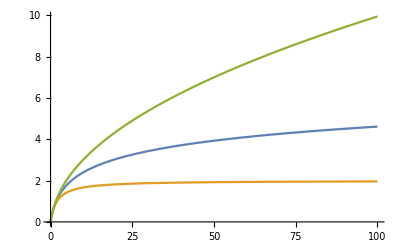

```mathematica
Plot[{Log[1+x],(2x)/(2+x),x/Sqrt[1+x]},{x,0,100}]
```

```mathematica
-2 k^2 m (2+m) (k+k m-4 R) R-2 (1+m) R (k m (2+m)-2 (1+m) R) μ/.k->R
```

-2 m (2+m) R^3 (-3 R+m R)-2 (1+m) R (-2 (1+m) R+m (2+m) R) μ

```mathematica
%//Simplify
```

-2 (-3+m) m (2+m) R^4-2 (1+m) (-2+m^2) R^2 μ

```mathematica
(k^2 (1+m)-4 k R+(1+m) (R^2+μ))/.k->R
```

-4 R^2+(1+m) R^2+(1+m) (R^2+μ)

```mathematica
%//Simplify
```

2 (-1+m) R^2+(1+m) μ

```mathematica
D[((1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ)))),k]
```

(2 k (1+m) (μ+m (2+m) (2 R^2+μ)))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))))-((1+m) (-(4 k (2 k (1+m)-2 R) R)/((k^2 (1+m)-2 k R+(1+m) (R^2+μ))^2)+(4 R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/(2 (k^2 (1+m)-2 k R+(1+m) (R^2+μ)) (1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ)))^(3/2))-((1+m) (2 k (1+m)-2 R) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ))^2 √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))))

```mathematica
%//Simplify
```

(4 k (1+m) R^2 (μ+2 m (R^2+μ)+m^2 (R^2+μ)) (k^2 (-1+2 m+m^2)+(1+m)^2 (R^2+μ)))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ))^2 (k^2 (1+m)+2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))))

```mathematica
((1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))))/.k->R
```

((1+m) ((1+m)^2 μ (R^2+μ)+R^2 (μ+m (2+m) (2 R^2+μ))))/((-2 R^2+(1+m) R^2+(1+m) (R^2+μ)) √(1+(4 R^2)/(-2 R^2+(1+m) R^2+(1+m) (R^2+μ))))

```mathematica
%/.R->(1+m)Sqrt[μ]
```

((1+m) ((1+m)^2 μ (μ+(1+m)^2 μ)+(1+m)^2 μ (μ+m (2+m) (μ+2 (1+m)^2 μ))))/(√(((1+m) μ+2 (1+m)^2 (2+m) μ)/(μ+m (μ+2 (1+m)^2 μ))) (μ+m (μ+2 (1+m)^2 μ)))

```mathematica
%//Simplify
```

((1+m)^2 √((5+6 m+2 m^2)/(1+2 m+2 m^2)) (3+8 m+12 m^2+8 m^3+2 m^4) μ)/(5+6 m+2 m^2)

```mathematica
Manipulate[Manipulate[Manipulate[Plot[L[R,2/(m+1)k,k^2+μ]/(2Pi^2 √((k^2 m (2+m))/(1+m)^2+μ)),{k,0,10R}],{R,(1+m)Sqrt[μ],10(1+m)Sqrt[μ]}],{μ,0.1,100}],{m,0.72,100}]
```

```mathematica
Manipulate[Manipulate[Plot[L[k(1+m)Sqrt[μ],2/(m+1)k(1+m)Sqrt[μ],(k(1+m)Sqrt[μ])^2+μ]/(2Pi^2 √(((k(1+m)Sqrt[μ])^2 m (2+m))/(1+m)^2+μ)),{m,0.72,100}],{k,1,10}],{μ,0.1,100}]
```

```mathematica
L[R,2/(m+1)k,k^2+μ]/(2Pi^2 √((k^2 m (2+m))/(1+m)^2+μ))
```

1/(8 k π √((k^2 m (2+m))/(1+m)^2+μ))(1+m) ((8 k R)/(1+m)+(4 k √(-(4 k^2)/(1+m)^2+4 (k^2+μ)) ArcTan[(-(2 k)/(1+m)+2 R)/(√(-(4 k^2)/(1+m)^2+4 (k^2+μ)))])/(1+m)+(4 k √(-(4 k^2)/(1+m)^2+4 (k^2+μ)) ArcTan[((2 k)/(1+m)+2 R)/(√(-(4 k^2)/(1+m)^2+4 (k^2+μ)))])/(1+m)-(4 k^2 Log[k^2-(2 k R)/(1+m)+R^2+μ])/(1+m)^2+2 R^2 Log[k^2-(2 k R)/(1+m)+R^2+μ]+2 (k^2+μ) Log[k^2-(2 k R)/(1+m)+R^2+μ]+(4 k^2 Log[k^2+(2 k R)/(1+m)+R^2+μ])/(1+m)^2-2 R^2 Log[k^2+(2 k R)/(1+m)+R^2+μ]-2 (k^2+μ) Log[k^2+(2 k R)/(1+m)+R^2+μ])

```mathematica
D[L[R,2/(m+1)k,k^2+μ]/(2Pi^2 √((k^2 m (2+m))/(1+m)^2+μ)),k]
```

1/(8 k π √((k^2 m (2+m))/(1+m)^2+μ))(1+m) ((8 R)/(1+m)-(4 k^2 (2 k-(2 R)/(1+m)))/((1+m)^2 (k^2-(2 k R)/(1+m)+R^2+μ))+(2 R^2 (2 k-(2 R)/(1+m)))/(k^2-(2 k R)/(1+m)+R^2+μ)+(2 (2 k-(2 R)/(1+m)) (k^2+μ))/(k^2-(2 k R)/(1+m)+R^2+μ)+(4 k^2 (2 k+(2 R)/(1+m)))/((1+m)^2 (k^2+(2 k R)/(1+m)+R^2+μ))-(2 R^2 (2 k+(2 R)/(1+m)))/(k^2+(2 k R)/(1+m)+R^2+μ)-(2 (2 k+(2 R)/(1+m)) (k^2+μ))/(k^2+(2 k R)/(1+m)+R^2+μ)+(4 k √(-(4 k^2)/(1+m)^2+4 (k^2+μ)) (-((8 k-(8 k)/(1+m)^2) (-(2 k)/(1+m)+2 R))/(2 (-(4 k^2)/(1+m)^2+4 (k^2+μ))^(3/2))-2/((1+m) √(-(4 k^2)/(1+m)^2+4 (k^2+μ)))))/((1+m) (1+(-(2 k)/(1+m)+2 R)^2/(-(4 k^2)/(1+m)^2+4 (k^2+μ))))+(4 k √(-(4 k^2)/(1+m)^2+4 (k^2+μ)) (-((8 k-(8 k)/(1+m)^2) ((2 k)/(1+m)+2 R))/(2 (-(4 k^2)/(1+m)^2+4 (k^2+μ))^(3/2))+2/((1+m) √(-(4 k^2)/(1+m)^2+4 (k^2+μ)))))/((1+m) (1+((2 k)/(1+m)+2 R)^2/(-(4 k^2)/(1+m)^2+4 (k^2+μ))))+(2 k (8 k-(8 k)/(1+m)^2) ArcTan[(-(2 k)/(1+m)+2 R)/(√(-(4 k^2)/(1+m)^2+4 (k^2+μ)))])/((1+m) √(-(4 k^2)/(1+m)^2+4 (k^2+μ)))+(4 √(-(4 k^2)/(1+m)^2+4 (k^2+μ)) ArcTan[(-(2 k)/(1+m)+2 R)/(√(-(4 k^2)/(1+m)^2+4 (k^2+μ)))])/(1+m)+(2 k (8 k-(8 k)/(1+m)^2) ArcTan[((2 k)/(1+m)+2 R)/(√(-(4 k^2)/(1+m)^2+4 (k^2+μ)))])/((1+m) √(-(4 k^2)/(1+m)^2+4 (k^2+μ)))+(4 √(-(4 k^2)/(1+m)^2+4 (k^2+μ)) ArcTan[((2 k)/(1+m)+2 R)/(√(-(4 k^2)/(1+m)^2+4 (k^2+μ)))])/(1+m)+4 k Log[k^2-(2 k R)/(1+m)+R^2+μ]-(8 k Log[k^2-(2 k R)/(1+m)+R^2+μ])/(1+m)^2-4 k Log[k^2+(2 k R)/(1+m)+R^2+μ]+(8 k Log[k^2+(2 k R)/(1+m)+R^2+μ])/(1+m)^2)-1/(8 (1+m) π ((k^2 m (2+m))/(1+m)^2+μ)^(3/2))m (2+m) ((8 k R)/(1+m)+(4 k √(-(4 k^2)/(1+m)^2+4 (k^2+μ)) ArcTan[(-(2 k)/(1+m)+2 R)/(√(-(4 k^2)/(1+m)^2+4 (k^2+μ)))])/(1+m)+(4 k √(-(4 k^2)/(1+m)^2+4 (k^2+μ)) ArcTan[((2 k)/(1+m)+2 R)/(√(-(4 k^2)/(1+m)^2+4 (k^2+μ)))])/(1+m)-(4 k^2 Log[k^2-(2 k R)/(1+m)+R^2+μ])/(1+m)^2+2 R^2 Log[k^2-(2 k R)/(1+m)+R^2+μ]+2 (k^2+μ) Log[k^2-(2 k R)/(1+m)+R^2+μ]+(4 k^2 Log[k^2+(2 k R)/(1+m)+R^2+μ])/(1+m)^2-2 R^2 Log[k^2+(2 k R)/(1+m)+R^2+μ]-2 (k^2+μ) Log[k^2+(2 k R)/(1+m)+R^2+μ])-1/(8 k^2 π √((k^2 m (2+m))/(1+m)^2+μ))(1+m) ((8 k R)/(1+m)+(4 k √(-(4 k^2)/(1+m)^2+4 (k^2+μ)) ArcTan[(-(2 k)/(1+m)+2 R)/(√(-(4 k^2)/(1+m)^2+4 (k^2+μ)))])/(1+m)+(4 k √(-(4 k^2)/(1+m)^2+4 (k^2+μ)) ArcTan[((2 k)/(1+m)+2 R)/(√(-(4 k^2)/(1+m)^2+4 (k^2+μ)))])/(1+m)-(4 k^2 Log[k^2-(2 k R)/(1+m)+R^2+μ])/(1+m)^2+2 R^2 Log[k^2-(2 k R)/(1+m)+R^2+μ]+2 (k^2+μ) Log[k^2-(2 k R)/(1+m)+R^2+μ]+(4 k^2 Log[k^2+(2 k R)/(1+m)+R^2+μ])/(1+m)^2-2 R^2 Log[k^2+(2 k R)/(1+m)+R^2+μ]-2 (k^2+μ) Log[k^2+(2 k R)/(1+m)+R^2+μ])

```mathematica
%//Simplify
```

(-4 k R (2 k^2 m (2+m)+(1+m)^2 μ)-(1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+2 m (2 R^2+μ)+m^2 (2 R^2+μ))) Log[k^2-(2 k R)/(1+m)+R^2+μ]+(1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+2 m (2 R^2+μ)+m^2 (2 R^2+μ))) Log[k^2+(2 k R)/(1+m)+R^2+μ])/(4 k^2 π √((k^2 m (2+m))/(1+m)^2+μ) (k^2 m (2+m)+(1+m)^2 μ))

```mathematica
%//FullSimplify
```

(-8 k^3 m (2+m) R-4 k (1+m)^2 R μ-(1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))) (Log[k^2-(2 k R)/(1+m)+R^2+μ]-Log[k^2+(2 k R)/(1+m)+R^2+μ]))/(4 k^2 π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
%50/.{Log[k^2-(2 k R)/(1+m)+R^2+μ]-Log[k^2+(2 k R)/(1+m)+R^2+μ]->-Log[(k^2+(2 k R)/(1+m)+R^2+μ)/(k^2-(2 k R)/(1+m)+R^2+μ)]}
```

(-8 k^3 m (2+m) R-4 k (1+m)^2 R μ+(1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))) Log[(k^2+(2 k R)/(1+m)+R^2+μ)/(k^2-(2 k R)/(1+m)+R^2+μ)])/(4 k^2 π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
%//FullSimplify
```

(-8 k^3 m (2+m) R-4 k (1+m)^2 R μ+(1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))) Log[1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))])/(4 k^2 π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
Log[(k^2+(2 k R)/(1+m)+R^2+μ)/(k^2-(2 k R)/(1+m)+R^2+μ)]//TeXForm
```

\log \left(\frac{k^2+\frac{2 k R}{m+1}+\mu +R^2}{k^2-\frac{2 k R}{m+1}+\mu +R^2}\right)

```mathematica
%54/.logineqgeq[[2]]
```

(-8 k^3 m (2+m) R-4 k (1+m)^2 R μ+(4 k (1+m) R ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ)))))/(4 k^2 π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
%//Simplify
```

(R (-2 k^2 m (2+m)-(1+m)^2 μ+((1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))))))/(k π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
%//FullSimplify
```

(R (-2 k^2 m (2+m)-(1+m)^2 μ+((1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))))))/(k π √((k^2 m (2+m))/(1+m)^2+μ) (μ+m (2+m) (k^2+μ)))

```mathematica
Limit[%59,R->Infinity]
```

0

```mathematica
%//TeXForm
```

\frac{R \left(\frac{(m+1) \left(k^2 \left(\mu +m (m+2) \left(\mu +2 R^2\right)\right)+\mu  (m+1)^2 \left(\mu +R^2\right)\right)}{\left(k^2 (m+1)-2 k R+(m+1) \left(\mu +R^2\right)\right) \sqrt{\frac{4 k
   R}{k^2 (m+1)-2 k R+(m+1) \left(\mu +R^2\right)}+1}}-2 k^2 m (m+2)-\mu  (m+1)^2\right)}{\pi  k \sqrt{\frac{k^2 m (m+2)}{(m+1)^2}+\mu } \left(m (m+2) \left(k^2+\mu \right)+\mu \right)}

```mathematica
logsim
```

{Log[x_] a_-Log[z_] a_→a Log[x/z]}

```mathematica
Series[((1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ)))),{R,Infinity,2}]
```

(4 k^2 m+2 k^2 m^2+μ+2 m μ+m^2 μ)-(2 (-2 k^4 m+3 k^4 m^2+4 k^4 m^3+k^4 m^4-k^2 μ+4 k^2 m^2 μ+4 k^2 m^3 μ+k^2 m^4 μ))/((1+m)^2 R^2)+O[1/R]^3

```mathematica
%//Simplify
```

(4 k^2 (1+m) R (k^2 m (2+m)+(1+m)^2 μ) (k^2 (1+m)^2+(-1+2 m+m^2) R^2+(1+m)^2 μ))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ))^2 (k^2 (1+m)+2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))))

```mathematica
%63//FullSimplify
```

(4 k^2 (1+m) R (μ+m (2+m) (k^2+μ)) (k^2 (1+m)^2-R^2+μ+m (2+m) (R^2+μ)))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ))^2 (k^2 (1+m)+2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ))))

```mathematica
%//TeXForm
```

\frac{4 k^2 (m+1) R \left(k^2 m (m+2)+\mu  (m+1)^2\right) \left(k^2 (m+1)^2+\left(m^2+2 m-1\right) R^2+\mu  (m+1)^2\right)}{\left(k^2 (m+1)-2 k R+(m+1) \left(\mu +R^2\right)\right)^2 \left(k^2 (m+1)+2 k
   R+(m+1) \left(\mu +R^2\right)\right) \sqrt{\frac{4 k R}{k^2 (m+1)-2 k R+(m+1) \left(\mu +R^2\right)}+1}}

```mathematica
Solve[-1+2 m+m^2==0,m]
```

{{m→-1-√2},{m→-1+√2}}

```mathematica
Limit[((1+m) ((1+m)^2 μ (R^2+μ)+k^2 (μ+m (2+m) (2 R^2+μ))))/((k^2 (1+m)-2 k R+(1+m) (R^2+μ)) √(1+(4 k R)/(k^2 (1+m)-2 k R+(1+m) (R^2+μ)))),R->Infinity]
```

2 k^2 m (2+m)+(1+m)^2 μ

```mathematica
L[R,2/(m+1)R,R^2+μ]/(2Pi^2 √((R^2 m (2+m))/(1+m)^2+μ))
```

1/(8 π R √((m (2+m) R^2)/(1+m)^2+μ))(1+m) ((8 R^2)/(1+m)+(4 R √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) ArcTan[(2 R-(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/(1+m)+(4 R √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) ArcTan[(2 R+(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/(1+m)+2 R^2 Log[2 R^2-(2 R^2)/(1+m)+μ]-(4 R^2 Log[2 R^2-(2 R^2)/(1+m)+μ])/(1+m)^2+2 (R^2+μ) Log[2 R^2-(2 R^2)/(1+m)+μ]-2 R^2 Log[2 R^2+(2 R^2)/(1+m)+μ]+(4 R^2 Log[2 R^2+(2 R^2)/(1+m)+μ])/(1+m)^2-2 (R^2+μ) Log[2 R^2+(2 R^2)/(1+m)+μ])

```mathematica
D[%,R]
```

1/(8 π R √((m (2+m) R^2)/(1+m)^2+μ))(1+m) ((16 R)/(1+m)+(2 R^2 (4 R-(4 R)/(1+m)))/(2 R^2-(2 R^2)/(1+m)+μ)-(4 R^2 (4 R-(4 R)/(1+m)))/((1+m)^2 (2 R^2-(2 R^2)/(1+m)+μ))+(2 (4 R-(4 R)/(1+m)) (R^2+μ))/(2 R^2-(2 R^2)/(1+m)+μ)-(2 R^2 (4 R+(4 R)/(1+m)))/(2 R^2+(2 R^2)/(1+m)+μ)+(4 R^2 (4 R+(4 R)/(1+m)))/((1+m)^2 (2 R^2+(2 R^2)/(1+m)+μ))-(2 (4 R+(4 R)/(1+m)) (R^2+μ))/(2 R^2+(2 R^2)/(1+m)+μ)+(4 R √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) (-((8 R-(8 R)/(1+m)^2) (2 R-(2 R)/(1+m)))/(2 (-(4 R^2)/(1+m)^2+4 (R^2+μ))^(3/2))+(2-2/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))))/((1+m) (1+(2 R-(2 R)/(1+m))^2/(-(4 R^2)/(1+m)^2+4 (R^2+μ))))+(4 R √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) (-((8 R-(8 R)/(1+m)^2) (2 R+(2 R)/(1+m)))/(2 (-(4 R^2)/(1+m)^2+4 (R^2+μ))^(3/2))+(2+2/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))))/((1+m) (1+(2 R+(2 R)/(1+m))^2/(-(4 R^2)/(1+m)^2+4 (R^2+μ))))+(2 R (8 R-(8 R)/(1+m)^2) ArcTan[(2 R-(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/((1+m) √(-(4 R^2)/(1+m)^2+4 (R^2+μ)))+(4 √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) ArcTan[(2 R-(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/(1+m)+(2 R (8 R-(8 R)/(1+m)^2) ArcTan[(2 R+(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/((1+m) √(-(4 R^2)/(1+m)^2+4 (R^2+μ)))+(4 √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) ArcTan[(2 R+(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/(1+m)+8 R Log[2 R^2-(2 R^2)/(1+m)+μ]-(8 R Log[2 R^2-(2 R^2)/(1+m)+μ])/(1+m)^2-8 R Log[2 R^2+(2 R^2)/(1+m)+μ]+(8 R Log[2 R^2+(2 R^2)/(1+m)+μ])/(1+m)^2)-1/(8 (1+m) π ((m (2+m) R^2)/(1+m)^2+μ)^(3/2))m (2+m) ((8 R^2)/(1+m)+(4 R √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) ArcTan[(2 R-(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/(1+m)+(4 R √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) ArcTan[(2 R+(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/(1+m)+2 R^2 Log[2 R^2-(2 R^2)/(1+m)+μ]-(4 R^2 Log[2 R^2-(2 R^2)/(1+m)+μ])/(1+m)^2+2 (R^2+μ) Log[2 R^2-(2 R^2)/(1+m)+μ]-2 R^2 Log[2 R^2+(2 R^2)/(1+m)+μ]+(4 R^2 Log[2 R^2+(2 R^2)/(1+m)+μ])/(1+m)^2-2 (R^2+μ) Log[2 R^2+(2 R^2)/(1+m)+μ])-1/(8 π R^2 √((m (2+m) R^2)/(1+m)^2+μ))(1+m) ((8 R^2)/(1+m)+(4 R √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) ArcTan[(2 R-(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/(1+m)+(4 R √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) ArcTan[(2 R+(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/(1+m)+2 R^2 Log[2 R^2-(2 R^2)/(1+m)+μ]-(4 R^2 Log[2 R^2-(2 R^2)/(1+m)+μ])/(1+m)^2+2 (R^2+μ) Log[2 R^2-(2 R^2)/(1+m)+μ]-2 R^2 Log[2 R^2+(2 R^2)/(1+m)+μ]+(4 R^2 Log[2 R^2+(2 R^2)/(1+m)+μ])/(1+m)^2-2 (R^2+μ) Log[2 R^2+(2 R^2)/(1+m)+μ])

```mathematica
%//Simplify
```

((1+m)^2 μ (4 R^2+(1+m) μ Log[(2 (2+m) R^2)/(1+m)+μ]-(1+m) μ Log[(2 m R^2+μ+m μ)/(1+m)]))/(4 π R^2 √((m (2+m) R^2)/(1+m)^2+μ) (μ+2 m (R^2+μ)+m^2 (R^2+μ)))

```mathematica
%//FullSimplify
```

(μ (4 R^2+(1+m) μ (-Log[(2 m R^2)/(1+m)+μ]+Log[(2 (2+m) R^2)/(1+m)+μ])))/(4 π R^2 ((m (2+m) R^2)/(1+m)^2+μ)^(3/2))

```mathematica
%71/.{-Log[(2 m R^2)/(1+m)+μ]+Log[(2 (2+m) R^2)/(1+m)+μ]->Log[((2 (2+m) R^2)/(1+m)+μ)/((2 m R^2)/(1+m)+μ)]}
```

(μ (4 R^2+(1+m) μ Log[((2 (2+m) R^2)/(1+m)+μ)/((2 m R^2)/(1+m)+μ)]))/(4 π R^2 ((m (2+m) R^2)/(1+m)^2+μ)^(3/2))

```mathematica
%77//TeXForm
```

\frac{\mu  \left(\mu  (m+1) \log \left(\frac{\mu +\frac{2 (m+2) R^2}{m+1}}{\mu +\frac{2 m R^2}{m+1}}\right)+4 R^2\right)}{4 \pi  R^2 \left(\mu +\frac{m (m+2) R^2}{(m+1)^2}\right)^{3/2}}

```mathematica
%/.logsim
```

(μ (4 R^2+(1+m) μ (-Log[(2 m R^2)/(1+m)+μ]+Log[(2 (2+m) R^2)/(1+m)+μ])))/(4 π R^2 ((m (2+m) R^2)/(1+m)^2+μ)^(3/2))

```mathematica
Manipulate[Manipulate[Plot[%68,{R,(1+m)Sqrt[μ],10000(1+m)Sqrt[μ]}],{m,0.72,10}],{μ,0.1,10}]
```

```mathematica
L[(1+m)Sqrt[μ],2/(m+1)(1+m)Sqrt[μ],((1+m)Sqrt[μ])^2+μ]/(2Pi^2 √((((1+m)Sqrt[μ])^2 m (2+m))/(1+m)^2+μ))
```

1/(8 π √μ √(μ+m (2+m) μ))(8 (1+m) μ+4 √μ √(-4 μ+4 (μ+(1+m)^2 μ)) ArcTan[(-2 √μ+2 (1+m) √μ)/(√(-4 μ+4 (μ+(1+m)^2 μ)))]+4 √μ √(-4 μ+4 (μ+(1+m)^2 μ)) ArcTan[(2 √μ+2 (1+m) √μ)/(√(-4 μ+4 (μ+(1+m)^2 μ)))]-4 μ Log[μ-2 (1+m) μ+2 (1+m)^2 μ]+2 (1+m)^2 μ Log[μ-2 (1+m) μ+2 (1+m)^2 μ]+2 (μ+(1+m)^2 μ) Log[μ-2 (1+m) μ+2 (1+m)^2 μ]+4 μ Log[μ+2 (1+m) μ+2 (1+m)^2 μ]-2 (1+m)^2 μ Log[μ+2 (1+m) μ+2 (1+m)^2 μ]-2 (μ+(1+m)^2 μ) Log[μ+2 (1+m) μ+2 (1+m)^2 μ])

```mathematica
%//Simplify
```

(4 ArcTan[(m √μ)/(√((1+m)^2 μ))]+4 ArcTan[((2+m) √μ)/(√((1+m)^2 μ))]+(√μ (4 (1+m)+(1+4 m+2 m^2) Log[(1+2 m+2 m^2) μ]-(1+4 m+2 m^2) Log[(5+6 m+2 m^2) μ]))/(√((1+m)^2 μ)))/(4 π)

```mathematica
%81//TeXForm
```

\frac{\frac{\sqrt{\mu } \left(\left(2 m^2+4 m+1\right) \log \left(\mu  \left(2 m^2+2 m+1\right)\right)-\left(2 m^2+4 m+1\right) \log \left(\mu  \left(2 m^2+6 m+5\right)\right)+4 (m+1)\right)}{\sqrt{\mu 
   (m+1)^2}}+4 \tan ^{-1}\left(\frac{\sqrt{\mu } m}{\sqrt{\mu  (m+1)^2}}\right)+4 \tan ^{-1}\left(\frac{\sqrt{\mu } (m+2)}{\sqrt{\mu  (m+1)^2}}\right)}{4 \pi }

```mathematica
D[%81,m]
```

((4 (-(m (1+m) μ^(3/2))/(((1+m)^2 μ)^(3/2))+(√μ)/(√((1+m)^2 μ))))/(1+m^2/(1+m)^2)+(4 (-((1+m) (2+m) μ^(3/2))/(((1+m)^2 μ)^(3/2))+(√μ)/(√((1+m)^2 μ))))/(1+(2+m)^2/(1+m)^2)+(√μ (4+((2+4 m) (1+4 m+2 m^2))/(1+2 m+2 m^2)-((6+4 m) (1+4 m+2 m^2))/(5+6 m+2 m^2)+(4+4 m) Log[(1+2 m+2 m^2) μ]-(4+4 m) Log[(5+6 m+2 m^2) μ]))/(√((1+m)^2 μ))-((1+m) μ^(3/2) (4 (1+m)+(1+4 m+2 m^2) Log[(1+2 m+2 m^2) μ]-(1+4 m+2 m^2) Log[(5+6 m+2 m^2) μ]))/(((1+m)^2 μ)^(3/2)))/(4 π)

```mathematica
%//Simplify
```

((1+m) μ^(3/2) (4 (1+m)+(3+4 m+2 m^2) Log[(1+2 m+2 m^2) μ]-(3+4 m+2 m^2) Log[(5+6 m+2 m^2) μ]))/(4 π ((1+m)^2 μ)^(3/2))

```mathematica
%//TeXForm
```

\frac{\mu ^{3/2} (m+1) \left(\left(2 m^2+4 m+3\right) \log \left(\mu  \left(2 m^2+2 m+1\right)\right)-\left(2 m^2+4 m+3\right) \log \left(\mu  \left(2 m^2+6 m+5\right)\right)+4 (m+1)\right)}{4 \pi 
   \left(\mu  (m+1)^2\right)^{3/2}}

```mathematica
%84//FullSimplify
```

```mathematica
((1+m) μ^(3/2) (4 (1+m)-(3+2 m (2+m))(2(4+4m)/(1+2 m (1+m)))/(2+(4+4m)/(1+2 m (1+m)))))/(4 π ((1+m)^2 μ)^(3/2))//TeXForm
```

\frac{\mu ^{3/2} (m+1) \left(4 (m+1)-\frac{2 (4 m+4) (2 m (m+2)+3)}{(2 m (m+1)+1) \left(\frac{4 m+4}{2 m (m+1)+1}+2\right)}\right)}{4 \pi  \left(\mu  (m+1)^2\right)^{3/2}}

```mathematica
%//Simplify
```

0

```mathematica
((1+m) μ^(3/2) (4 (1+m)-(3+2 m (2+m)) ((2(5+2 m (3+m)) μ)/(μ+2 m (1+m) μ))/(2+((5+2 m (3+m)) μ)/(μ+2 m (1+m) μ))))/(4 π ((1+m)^2 μ)^(3/2))
```

((1+m) μ^(3/2) (4 (1+m)-(2 (3+2 m (2+m)) (5+2 m (3+m)) μ)/((μ+2 m (1+m) μ) (2+((5+2 m (3+m)) μ)/(μ+2 m (1+m) μ)))))/(4 π ((1+m)^2 μ)^(3/2))

```mathematica
%//Simplify
```

-((1+m) (1+2 m+2 m^2)^2 μ^(3/2))/(2 (7+10 m+6 m^2) π ((1+m)^2 μ)^(3/2))

```mathematica
%//FullSimplify
```

((1+m) μ^(3/2) (4 (1+m)-(3+2 m (2+m)) Log[(5+2 m (3+m))/(1+2 m (1+m))]))/(4 π ((1+m)^2 μ)^(3/2))

```mathematica
D[(5+2 m (3+m))/(1+2 m (1+m)),m]
```

(2 m+2 (3+m))/(1+2 m (1+m))-((2 m+2 (1+m)) (5+2 m (3+m)))/(1+2 m (1+m))^2

```mathematica
Solve[%==0,m]
```

{{m→1/2 (-2-√2)},{m→1/2 (-2+√2)}}

```mathematica
%//N
```

{{m→-1.70711},{m→-0.292893}}

```mathematica
%//.{-(3+2 m (2+m)) Log[(5+2 m (3+m)) μ]+(3+2 m (2+m)) Log[μ+2 m (1+m) μ]->-(3+2 m (2+m))Log[((5+2 m (3+m)) μ)/(μ+2 m (1+m) μ)]}
```

((1+m) μ^(3/2) (4 (1+m)-(3+2 m (2+m)) Log[(5+2 m (3+m)) μ]+(3+2 m (2+m)) Log[μ+2 m (1+m) μ]))/(4 π ((1+m)^2 μ)^(3/2))

```mathematica
L[R,2/(m+1)R,R^2+μ]/(2Pi^2 √((R^2 m (2+m))/(1+m)^2+μ))
```

1/(8 π R √((m (2+m) R^2)/(1+m)^2+μ))(1+m) ((8 R^2)/(1+m)+(4 R √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) ArcTan[(2 R-(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/(1+m)+(4 R √(-(4 R^2)/(1+m)^2+4 (R^2+μ)) ArcTan[(2 R+(2 R)/(1+m))/(√(-(4 R^2)/(1+m)^2+4 (R^2+μ)))])/(1+m)+2 R^2 Log[2 R^2-(2 R^2)/(1+m)+μ]-(4 R^2 Log[2 R^2-(2 R^2)/(1+m)+μ])/(1+m)^2+2 (R^2+μ) Log[2 R^2-(2 R^2)/(1+m)+μ]-2 R^2 Log[2 R^2+(2 R^2)/(1+m)+μ]+(4 R^2 Log[2 R^2+(2 R^2)/(1+m)+μ])/(1+m)^2-2 (R^2+μ) Log[2 R^2+(2 R^2)/(1+m)+μ])

```mathematica
%//Simplify
```

1/(8 π R √((m (2+m) R^2)/(1+m)^2+μ))(1+m) ((8 R^2)/(1+m)+(8 R √((μ+2 m (R^2+μ)+m^2 (R^2+μ))/(1+m)^2) ArcTan[(m R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))])/(1+m)+(8 R √((μ+2 m (R^2+μ)+m^2 (R^2+μ))/(1+m)^2) ArcTan[((2+m) R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))])/(1+m)-4 R^2 Log[(2 (2+m) R^2)/(1+m)+μ]+(4 R^2 Log[(2 (2+m) R^2)/(1+m)+μ])/(1+m)^2-2 μ Log[(2 (2+m) R^2)/(1+m)+μ]+4 R^2 Log[(2 m R^2+μ+m μ)/(1+m)]-(4 R^2 Log[(2 m R^2+μ+m μ)/(1+m)])/(1+m)^2+2 μ Log[(2 m R^2+μ+m μ)/(1+m)])

```mathematica
%//FullSimplify
```

((4 R)/(√((m (2+m) R^2)/(1+m)^2+μ))+4 ArcTan[(m R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))]+4 ArcTan[((2+m) R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))]+((μ+m (2+m) (2 R^2+μ)) (Log[(2 m R^2)/(1+m)+μ]-Log[(2 (2+m) R^2)/(1+m)+μ]))/((1+m) R √((m (2+m) R^2)/(1+m)^2+μ)))/(4 π)

```mathematica
%103/.
```

((4 R)/(√((m (2+m) R^2)/(1+m)^2+μ))+4 ArcTan[(m R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))]+4 ArcTan[((2+m) R)/((1+m) √((m (2+m) R^2)/(1+m)^2+μ))]+((μ+m (2+m) (2 R^2+μ)) (Log[(2 m R^2)/(1+m)+μ]-Log[(2 (2+m) R^2)/(1+m)+μ]))/((1+m) R √((m (2+m) R^2)/(1+m)^2+μ)))/(4 π)

```mathematica
%/.R->(1+m)Sqrt[μ]
```

```mathematica
Manipulate[Manipulate[Manipulate[Manipulate[Plot[L[R,2/(1+m)Abs[Sum[Subscript[k, i],{i,1,N-1}]],Sum[Subscript[k, i]^2,{i,1,N-1}]-(2m)/(m+1)Sum[Sum[Subscript[k, i]·Subscript[k, j],{j,i+1,N-1}],{i,1,N-2}]+μ]/√(-(4 S^2)/(1+m)^2+4 (S^2-(2 m T)/(1+m)+μ)),{m,0.72,100}],{R,1,100}],{T,0,S^2/2}],{S,0,100}],{μ,0.1,100}]
```

```mathematica
L[R,2/(1+m)S,S^2-(2m)/(m+1)*T+μ]
```

1/(4 S)(1+m) π ((8 R S)/(1+m)+(4 S √(-(4 S^2)/(1+m)^2+4 (S^2-(2 m T)/(1+m)+μ)) ArcTan[(2 R-(2 S)/(1+m))/(√(-(4 S^2)/(1+m)^2+4 (S^2-(2 m T)/(1+m)+μ)))])/(1+m)+(4 S √(-(4 S^2)/(1+m)^2+4 (S^2-(2 m T)/(1+m)+μ)) ArcTan[(2 R+(2 S)/(1+m))/(√(-(4 S^2)/(1+m)^2+4 (S^2-(2 m T)/(1+m)+μ)))])/(1+m)+2 R^2 Log[R^2-(2 R S)/(1+m)+S^2-(2 m T)/(1+m)+μ]-(4 S^2 Log[R^2-(2 R S)/(1+m)+S^2-(2 m T)/(1+m)+μ])/(1+m)^2+2 (S^2-(2 m T)/(1+m)+μ) Log[R^2-(2 R S)/(1+m)+S^2-(2 m T)/(1+m)+μ]-2 R^2 Log[R^2+(2 R S)/(1+m)+S^2-(2 m T)/(1+m)+μ]+(4 S^2 Log[R^2+(2 R S)/(1+m)+S^2-(2 m T)/(1+m)+μ])/(1+m)^2-2 (S^2-(2 m T)/(1+m)+μ) Log[R^2+(2 R S)/(1+m)+S^2-(2 m T)/(1+m)+μ])

```mathematica
L[R,2/(1+m)Sqrt[Sum[Subscript[k, i],{i,1,N-1}]^2],Sum[Subscript[k, i]^2,{i,1,N-1}]-(2m)/(m+1)Sum[Sum[Subscript[k, i]·Subscript[k, j],{j,i+1,N-1}],{i,1,N-2}]+μ]
```

1/(4 √((∑_(i=1)^(-1+N) k_i)^2))(1+m) π (2 R^2 Log[R^2+μ-(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)]-2 R^2 Log[R^2+μ+(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)]-(4 Log[R^2+μ-(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)] (∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+(4 Log[R^2+μ+(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)] (∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+(8 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+2 Log[R^2+μ-(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)] (μ+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m))-2 Log[R^2+μ+(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)] (μ+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m))+(4 ArcTan[(2 R-(2 √((∑_(i=1)^(-1+N) k_i)^2))/(1+m))/(√(-(4 (∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+4 (μ+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m))))] √((∑_(i=1)^(-1+N) k_i)^2) √(-(4 (∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+4 (μ+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m))))/(1+m)+(4 ArcTan[(2 R+(2 √((∑_(i=1)^(-1+N) k_i)^2))/(1+m))/(√(-(4 (∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+4 (μ+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m))))] √((∑_(i=1)^(-1+N) k_i)^2) √(-(4 (∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+4 (μ+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m))))/(1+m))

```mathematica
%//Simplify
```

1/(4 √((∑_(i=1)^(-1+N) k_i)^2))(1+m) π (2 R^2 Log[R^2+μ-(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)]-2 R^2 Log[R^2+μ+(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)]-(4 Log[R^2+μ-(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)] (∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+(4 Log[R^2+μ+(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)] (∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+(8 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+2 Log[R^2+μ-(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)] (μ+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m))-2 Log[R^2+μ+(2 R √((∑_(i=1)^(-1+N) k_i)^2))/(1+m)+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)] (μ+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m))+(8 ArcTan[(R+m R-√((∑_(i=1)^(-1+N) k_i)^2))/((1+m) √(μ-((∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)))] √((∑_(i=1)^(-1+N) k_i)^2) √(μ-((∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)))/(1+m)+(8 ArcTan[(R+(√((∑_(i=1)^(-1+N) k_i)^2))/(1+m))/(√(μ-((∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)))] √((∑_(i=1)^(-1+N) k_i)^2) √(μ-((∑_(i=1)^(-1+N) k_i)^2)/(1+m)^2+∑_(i=1)^(-1+N) k_i^2-(2 m ∑_(i=1)^(-2+N) (∑_(j=1+i)^(-1+N) k_i·k_j))/(1+m)))/(1+m))

```mathematica
%//FullSimplify
```

$Aborted

```mathematica
L[R,y,α]
```

(π (4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α]))/(2 y)

```mathematica
%//Simplify
```

(π (4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α]))/(2 y)

```mathematica
%//FullSimplify
```

1/2 π (4 R+2 √(-y^2+4 α) (-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))])+((2 R^2-y^2+2 α) (Log[R^2-R y+α]-Log[R (R+y)+α]))/y)

```mathematica
D[%130,α]
```

1/2 π (((2 R^2-y^2+2 α) (1/(R^2-R y+α)-1/(R (R+y)+α)))/y+2 √(-y^2+4 α) ((2 (-2 R+y))/((-y^2+4 α)^(3/2) (1+(-2 R+y)^2/(-y^2+4 α)))-(2 (2 R+y))/((-y^2+4 α)^(3/2) (1+(2 R+y)^2/(-y^2+4 α))))+(4 (-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))]))/(√(-y^2+4 α))+(2 (Log[R^2-R y+α]-Log[R (R+y)+α]))/y)

```mathematica
%//Simplify
```

(π (2 y √(-y^2+4 α) ArcTan[(-2 R+y)/(√(-y^2+4 α))]-2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+(y^2-4 α) (Log[R^2-R y+α]-Log[R (R+y)+α])))/(y^3-4 y α)

```mathematica
D[L[R,y,α]/Sqrt[4α-y^2],y]
```

1/(2 y √(-y^2+4 α))π (4 R-(2 R^3)/(R^2-R y+α)+(R y^2)/(R^2-R y+α)-(2 R α)/(R^2-R y+α)-(2 R^3)/(R^2+R y+α)+(R y^2)/(R^2+R y+α)-(2 R α)/(R^2+R y+α)+(2 y √(-y^2+4 α) (((2 R-y) y)/((-y^2+4 α)^(3/2))-1/(√(-y^2+4 α))))/(1+(2 R-y)^2/(-y^2+4 α))+(2 y √(-y^2+4 α) ((y (2 R+y))/((-y^2+4 α)^(3/2))+1/(√(-y^2+4 α))))/(1+(2 R+y)^2/(-y^2+4 α))-(2 y^2 ArcTan[(2 R-y)/(√(-y^2+4 α))])/(√(-y^2+4 α))+2 √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]-(2 y^2 ArcTan[(2 R+y)/(√(-y^2+4 α))])/(√(-y^2+4 α))+2 √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]-2 y Log[R^2-R y+α]+2 y Log[R^2+R y+α])+(π (4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α]))/(2 (-y^2+4 α)^(3/2))-(π (4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α]))/(2 y^2 √(-y^2+4 α))

```mathematica
%//Simplify
```

(2 π (2 R y (y^2-2 α)+(R^2 (y^2-2 α)-2 α^2) Log[R^2-R y+α]+(-R^2 (y^2-2 α)+2 α^2) Log[R^2+R y+α]))/(y^2 (-y^2+4 α)^(3/2))

```mathematica
D[L[R,y,α]/Sqrt[4α-y^2],y]
```

1/(2 y √(-y^2+4 α))π (4 R-(2 R^3)/(R^2-R y+α)+(R y^2)/(R^2-R y+α)-(2 R α)/(R^2-R y+α)-(2 R^3)/(R^2+R y+α)+(R y^2)/(R^2+R y+α)-(2 R α)/(R^2+R y+α)+(2 y √(-y^2+4 α) (((2 R-y) y)/((-y^2+4 α)^(3/2))-1/(√(-y^2+4 α))))/(1+(2 R-y)^2/(-y^2+4 α))+(2 y √(-y^2+4 α) ((y (2 R+y))/((-y^2+4 α)^(3/2))+1/(√(-y^2+4 α))))/(1+(2 R+y)^2/(-y^2+4 α))-(2 y^2 ArcTan[(2 R-y)/(√(-y^2+4 α))])/(√(-y^2+4 α))+2 √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]-(2 y^2 ArcTan[(2 R+y)/(√(-y^2+4 α))])/(√(-y^2+4 α))+2 √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]-2 y Log[R^2-R y+α]+2 y Log[R^2+R y+α])+1/(2 (-y^2+4 α)^(3/2))π (4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α])-1/(2 y^2 √(-y^2+4 α))π (4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α])

```mathematica
%//Simplify
```

(2 π (2 R y (y^2-2 α)+(R^2 (y^2-2 α)-2 α^2) Log[R^2-R y+α]+(-R^2 (y^2-2 α)+2 α^2) Log[R^2+R y+α]))/(y^2 (-y^2+4 α)^(3/2))

```mathematica
%//FullSimplify
```

-(-4 π R y (y^2-2 α)-2 π (R^2 (y^2-2 α)-2 α^2) (Log[R^2-R y+α]-Log[R (R+y)+α]))/(y^2 (-y^2+4 α)^(3/2))

```mathematica
%/.{Log[R^2-R y+α]-Log[R (R+y)+α]->-Log[1+(2R*y)/(R^2-R y+α)]}
```

-(-4 π R y (y^2-2 α)+2 π (R^2 (y^2-2 α)-2 α^2) Log[1+(2 R y)/(R^2-R y+α)])/(y^2 (-y^2+4 α)^(3/2))

```mathematica
%143/.logineqgeq[[2]]
```

-(-4 π R y (y^2-2 α)+(4 π R y (R^2 (y^2-2 α)-2 α^2))/((R^2-R y+α) √(1+(2 R y)/(R^2-R y+α))))/(y^2 (-y^2+4 α)^(3/2))

```mathematica
%//Simplify
```

-(4 π R (-y^2+2 α+(√((R^2+R y+α)/(R^2-R y+α)) (R^2 (y^2-2 α)-2 α^2))/(R^2+R y+α)))/(y (-y^2+4 α)^(3/2))

```mathematica
%//FullSimplify
```

-(4 π R (-y^2+2 α+((R^2 (y^2-2 α)-2 α^2) √(1+(2 R y)/(R^2-R y+α)))/(R (R+y)+α)))/(y (-y^2+4 α)^(3/2))

```mathematica
L[R,y+x,α+(1+m)/4(x^2+2y*x)+(1+m)^2/4 x^2]
```

1/(2 (x+y))π (4 R (x+y)+2 (x+y) √(-(x+y)^2+4 (1/4 (1+m)^2 x^2+1/4 (1+m) (x^2+2 x y)+α)) ArcTan[(2 R-x-y)/(√(-(x+y)^2+4 (1/4 (1+m)^2 x^2+1/4 (1+m) (x^2+2 x y)+α)))]+2 (x+y) √(-(x+y)^2+4 (1/4 (1+m)^2 x^2+1/4 (1+m) (x^2+2 x y)+α)) ArcTan[(2 R+x+y)/(√(-(x+y)^2+4 (1/4 (1+m)^2 x^2+1/4 (1+m) (x^2+2 x y)+α)))]+2 R^2 Log[R^2+1/4 (1+m)^2 x^2-R (x+y)+1/4 (1+m) (x^2+2 x y)+α]-(x+y)^2 Log[R^2+1/4 (1+m)^2 x^2-R (x+y)+1/4 (1+m) (x^2+2 x y)+α]+2 (1/4 (1+m)^2 x^2+1/4 (1+m) (x^2+2 x y)+α) Log[R^2+1/4 (1+m)^2 x^2-R (x+y)+1/4 (1+m) (x^2+2 x y)+α]-2 R^2 Log[R^2+1/4 (1+m)^2 x^2+R (x+y)+1/4 (1+m) (x^2+2 x y)+α]+(x+y)^2 Log[R^2+1/4 (1+m)^2 x^2+R (x+y)+1/4 (1+m) (x^2+2 x y)+α]-2 (1/4 (1+m)^2 x^2+1/4 (1+m) (x^2+2 x y)+α) Log[R^2+1/4 (1+m)^2 x^2+R (x+y)+1/4 (1+m) (x^2+2 x y)+α])

```mathematica
L[R,y,α]//FullSimplify
```

1/2 π (4 R+2 √(-y^2+4 α) (-ArcTan[(-2 R+y)/(√(-y^2+4 α))]+ArcTan[(2 R+y)/(√(-y^2+4 α))])+((2 R^2-y^2+2 α) (Log[R^2-R y+α]-Log[R (R+y)+α]))/y)

```mathematica
%/.{y->y+x,α->α+(1+m)/4(x^2+2y*x)+(1+m)^2/4 x^2}
```

1/2 π (4 R+2 √(-(x+y)^2+4 (1/4 (1+m)^2 x^2+1/4 (1+m) (x^2+2 x y)+α)) (-ArcTan[(-2 R+x+y)/(√(-(x+y)^2+4 (1/4 (1+m)^2 x^2+1/4 (1+m) (x^2+2 x y)+α)))]+ArcTan[(2 R+x+y)/(√(-(x+y)^2+4 (1/4 (1+m)^2 x^2+1/4 (1+m) (x^2+2 x y)+α)))])+((2 R^2-(x+y)^2+2 (1/4 (1+m)^2 x^2+1/4 (1+m) (x^2+2 x y)+α)) (Log[R^2+1/4 (1+m)^2 x^2-R (x+y)+1/4 (1+m) (x^2+2 x y)+α]-Log[1/4 (1+m)^2 x^2+R (R+x+y)+1/4 (1+m) (x^2+2 x y)+α]))/(x+y))

```mathematica
%//FullSimplify
```

2 π R+π √(m (2+m) x^2+2 m x y-y^2+4 α) (-ArcTan[(-2 R+x+y)/(√(m (2+m) x^2+2 m x y-y^2+4 α))]+ArcTan[(2 R+x+y)/(√(m (2+m) x^2+2 m x y-y^2+4 α))])+(π (4 R^2+(-1+m (2+m)) x^2+2 (-1+m) x y-2 y^2+4 α) (Log[R^2-R (x+y)+1/4 (1+m) x (x+m x+2 y)+α]-Log[R^2+R (x+y)+1/4 (1+m) x (x+m x+2 y)+α]))/(4 (x+y))

```mathematica
D[%30,x]
```

(π (4 R^2+(-1+m (2+m)) x^2+2 (-1+m) x y-2 y^2+4 α) ((-R+1/4 (1+m)^2 x+1/4 (1+m) (x+m x+2 y))/(R^2-R (x+y)+1/4 (1+m) x (x+m x+2 y)+α)-(R+1/4 (1+m)^2 x+1/4 (1+m) (x+m x+2 y))/(R^2+R (x+y)+1/4 (1+m) x (x+m x+2 y)+α)))/(4 (x+y))+π √(m (2+m) x^2+2 m x y-y^2+4 α) (-(-((-2 R+x+y) (2 m (2+m) x+2 m y))/(2 (m (2+m) x^2+2 m x y-y^2+4 α)^(3/2))+1/(√(m (2+m) x^2+2 m x y-y^2+4 α)))/(1+(-2 R+x+y)^2/(m (2+m) x^2+2 m x y-y^2+4 α))+(-((2 R+x+y) (2 m (2+m) x+2 m y))/(2 (m (2+m) x^2+2 m x y-y^2+4 α)^(3/2))+1/(√(m (2+m) x^2+2 m x y-y^2+4 α)))/(1+(2 R+x+y)^2/(m (2+m) x^2+2 m x y-y^2+4 α)))+(π (2 m (2+m) x+2 m y) (-ArcTan[(-2 R+x+y)/(√(m (2+m) x^2+2 m x y-y^2+4 α))]+ArcTan[(2 R+x+y)/(√(m (2+m) x^2+2 m x y-y^2+4 α))]))/(2 √(m (2+m) x^2+2 m x y-y^2+4 α))+(π (2 (-1+m (2+m)) x+2 (-1+m) y) (Log[R^2-R (x+y)+1/4 (1+m) x (x+m x+2 y)+α]-Log[R^2+R (x+y)+1/4 (1+m) x (x+m x+2 y)+α]))/(4 (x+y))-(π (4 R^2+(-1+m (2+m)) x^2+2 (-1+m) x y-2 y^2+4 α) (Log[R^2-R (x+y)+1/4 (1+m) x (x+m x+2 y)+α]-Log[R^2+R (x+y)+1/4 (1+m) x (x+m x+2 y)+α]))/(4 (x+y)^2)

```mathematica
%//FullSimplify
```

$Aborted

```mathematica
Manipulate[Manipulate[Manipulate[Manipulate[Plot[%,{x,-10,10}],{α,(1+m)y^2/4,1000}],{y,0.01,100}],{R,1,1000}],{m,0.01,10}]
```

```mathematica
Manipulate[Manipulate[Manipulate[Plot[{L[R,y,α],Pi^2 √(-y^2+4 α)},{R,0,100000}],{α,(1+m)y^2/4,10(1+m)y^2/4}],{y,10,100}],{m,0.01,1}]
```

```mathematica
L[R,y,α]
```

(π (4 R y+2 y √(-y^2+4 α) ArcTan[(2 R-y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+2 R^2 Log[R^2-R y+α]-y^2 Log[R^2-R y+α]+2 α Log[R^2-R y+α]-2 R^2 Log[R^2+R y+α]+y^2 Log[R^2+R y+α]-2 α Log[R^2+R y+α]))/(2 y)

```mathematica
Manipulate[Manipulate[Manipulate[Plot[{L[R,y,μ],2*Pi^2*Sqrt[μ]},{R,1,100}],{y,0.1,100}],{m,0.01,1}],{μ,1,100}]
```

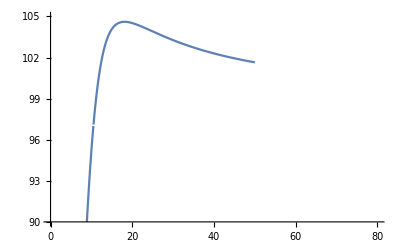

```mathematica
Plot[{L[R,21,135.3]},{R,0,50},PlotRange->{{0,80},{90,105}}]
```

```mathematica
Maximize[{L[R,y,(1+0.1)y^2/4*k]/(Pi^2Sqrt[(1+0.1)y^2*k-y^2]),0<y,1<R,k>1},{y,R,k}]
```

{1.36808,{y→1.94654,R→1.04311,k→1.}}

```mathematica
Manipulate[Maximize[L[R,y,(1+0.1)y^2/4+1]/Sqrt[y^2+1],{{y,R}}],{y,0.001,10000}]
```

```mathematica
Pi^2Sqrt[(1+0.1)1000^2+0.004-1000^2]
```

3121.04

```mathematica
%//N
```

{80.7605,{R→9.07861}}

```mathematica
Pi^2Sqrt[4*112-21^2]//N
```

26.1125

```mathematica
Series[L[R,y,α],{R,Infinity,0}]
```

(1/(-y^2+4 α))^(1/2 Floor[Arg[-(4 R y)/(y^2-4 α)-y^2/(y^2-4 α)]/(2 π)]) (-y^2+4 α)^(1/2 Floor[Arg[-(4 R y)/(y^2-4 α)-y^2/(y^2-4 α)]/(2 π)]) (-1/2 π^2 √(-1/(y^2-4 α)) (y^2-4 α)+O[1/R]^5)+(1/(-y^2+4 α))^(1/2 Floor[Arg[(4 R y)/(y^2-4 α)-y^2/(y^2-4 α)]/(2 π)]) (-y^2+4 α)^(1/2 Floor[Arg[(4 R y)/(y^2-4 α)-y^2/(y^2-4 α)]/(2 π)]) (-1/2 π^2 √(-1/(y^2-4 α)) (y^2-4 α)+O[1/R]^5)+((4 π (y^2-3 α))/(3 R)+(4 π (y^4-5 y^2 α+5 α^2))/(15 R^3)+O[1/R]^4)

```mathematica
Integrate[x^2(x^2+y*k*x),{x,0,N}]
```

N^5/5+1/4 k N^4 y

```mathematica
2*Pi*Integrate[%,{k,-1,1}]
```

(4 N^5 π)/5

```mathematica
((4/3 Pi*n^3)^2)/(4Pi n)
```

(4 n^5 π)/9

```mathematica
L[R/n,y/n,α/n^2]
```

(n π ((4 R y)/n^2+(2 y √(-y^2/n^2+(4 α)/n^2) ArcTan[((2 R)/n-y/n)/(√(-y^2/n^2+(4 α)/n^2))])/n+(2 y √(-y^2/n^2+(4 α)/n^2) ArcTan[((2 R)/n+y/n)/(√(-y^2/n^2+(4 α)/n^2))])/n+(2 R^2 Log[R^2/n^2-(R y)/n^2+α/n^2])/n^2-(y^2 Log[R^2/n^2-(R y)/n^2+α/n^2])/n^2+(2 α Log[R^2/n^2-(R y)/n^2+α/n^2])/n^2-(2 R^2 Log[R^2/n^2+(R y)/n^2+α/n^2])/n^2+(y^2 Log[R^2/n^2+(R y)/n^2+α/n^2])/n^2-(2 α Log[R^2/n^2+(R y)/n^2+α/n^2])/n^2))/(2 y)

```mathematica
%//FullSimplify
```

(π (4 R y-2 y √(-y^2+4 α) ArcTan[(-2 R+y)/(√(-y^2+4 α))]+2 y √(-y^2+4 α) ArcTan[(2 R+y)/(√(-y^2+4 α))]+(2 R^2-y^2+2 α) (Log[(R^2-R y+α)/n^2]-Log[(R (R+y)+α)/n^2])))/(2 n y)

```mathematica
Manipulate[Manipulate[Manipulate[Plot[{L[R,y,(1+m)y^2/4+μ],2*Pi^2Sqrt[μ]},{R,0.5,10000}],{y,0.1,100}],{m,0.01,1}],{μ,0.1,1000}]
```

```mathematica
Manipulate[L[1,0.01,μ]/Sqrt[μ],{μ,0,1}]
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
Limit[L[1,y,(1+m)y^2/4+μ]/Sqrt[μ],y->0 ]
```

$Aborted

```mathematica
Limit[L[2,y,(1+m)y^2/4+μ],y->0]
```

4 π √μ ArcTan[2/(√μ)]

```mathematica
D[L[R,y,(1+m)y^2/4+μ],y]
```

1/(2 y)π (4 R+(2 R^2 (-R+1/2 (1+m) y))/(R^2-R y+1/4 (1+m) y^2+μ)-(y^2 (-R+1/2 (1+m) y))/(R^2-R y+1/4 (1+m) y^2+μ)+(2 (-R+1/2 (1+m) y) (1/4 (1+m) y^2+μ))/(R^2-R y+1/4 (1+m) y^2+μ)-(2 R^2 (R+1/2 (1+m) y))/(R^2+R y+1/4 (1+m) y^2+μ)+(y^2 (R+1/2 (1+m) y))/(R^2+R y+1/4 (1+m) y^2+μ)-(2 (R+1/2 (1+m) y) (1/4 (1+m) y^2+μ))/(R^2+R y+1/4 (1+m) y^2+μ)+(2 y √(-y^2+4 (1/4 (1+m) y^2+μ)) (-((2 R-y) (-2 y+2 (1+m) y))/(2 (-y^2+4 (1/4 (1+m) y^2+μ))^(3/2))-1/(√(-y^2+4 (1/4 (1+m) y^2+μ)))))/(1+(2 R-y)^2/(-y^2+4 (1/4 (1+m) y^2+μ)))+(2 y √(-y^2+4 (1/4 (1+m) y^2+μ)) (-((2 R+y) (-2 y+2 (1+m) y))/(2 (-y^2+4 (1/4 (1+m) y^2+μ))^(3/2))+1/(√(-y^2+4 (1/4 (1+m) y^2+μ)))))/(1+(2 R+y)^2/(-y^2+4 (1/4 (1+m) y^2+μ)))+(y (-2 y+2 (1+m) y) ArcTan[(2 R-y)/(√(-y^2+4 (1/4 (1+m) y^2+μ)))])/(√(-y^2+4 (1/4 (1+m) y^2+μ)))+2 √(-y^2+4 (1/4 (1+m) y^2+μ)) ArcTan[(2 R-y)/(√(-y^2+4 (1/4 (1+m) y^2+μ)))]+(y (-2 y+2 (1+m) y) ArcTan[(2 R+y)/(√(-y^2+4 (1/4 (1+m) y^2+μ)))])/(√(-y^2+4 (1/4 (1+m) y^2+μ)))+2 √(-y^2+4 (1/4 (1+m) y^2+μ)) ArcTan[(2 R+y)/(√(-y^2+4 (1/4 (1+m) y^2+μ)))]-2 y Log[R^2-R y+1/4 (1+m) y^2+μ]+(1+m) y Log[R^2-R y+1/4 (1+m) y^2+μ]+2 y Log[R^2+R y+1/4 (1+m) y^2+μ]-(1+m) y Log[R^2+R y+1/4 (1+m) y^2+μ])-1/(2 y^2)π (4 R y+2 y √(-y^2+4 (1/4 (1+m) y^2+μ)) ArcTan[(2 R-y)/(√(-y^2+4 (1/4 (1+m) y^2+μ)))]+2 y √(-y^2+4 (1/4 (1+m) y^2+μ)) ArcTan[(2 R+y)/(√(-y^2+4 (1/4 (1+m) y^2+μ)))]+2 R^2 Log[R^2-R y+1/4 (1+m) y^2+μ]-y^2 Log[R^2-R y+1/4 (1+m) y^2+μ]+2 (1/4 (1+m) y^2+μ) Log[R^2-R y+1/4 (1+m) y^2+μ]-2 R^2 Log[R^2+R y+1/4 (1+m) y^2+μ]+y^2 Log[R^2+R y+1/4 (1+m) y^2+μ]-2 (1/4 (1+m) y^2+μ) Log[R^2+R y+1/4 (1+m) y^2+μ])

```mathematica
%//FullSimplify
```

(m π y ArcTan[(2 R-y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(m π y ArcTan[(2 R+y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(π (-8 R y-(4 R^2+y^2-m y^2+4 μ) (Log[R^2-R y+1/4 (1+m) y^2+μ]-Log[R^2+R y+1/4 (1+m) y^2+μ])))/(4 y^2)

```mathematica
%//FullSimplify
```

```mathematica
D[(m π y ArcTan[(2 R-y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(m π y ArcTan[(2 R+y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(π (-8 R y-(4 R^2+y^2-m y^2+4 μ) (Log[R^2-R y+1/4 (1+m) y^2+μ]-Log[R^2+R y+1/4 (1+m) y^2+μ])))/(4 y^2),y]
```

(m π y (-(m (2 R-y) y)/((m y^2+4 μ)^(3/2))-1/(√(m y^2+4 μ))))/(√(m y^2+4 μ) (1+(2 R-y)^2/(m y^2+4 μ)))+(m π y (-(m y (2 R+y))/((m y^2+4 μ)^(3/2))+1/(√(m y^2+4 μ))))/(√(m y^2+4 μ) (1+(2 R+y)^2/(m y^2+4 μ)))-(m^2 π y^2 ArcTan[(2 R-y)/(√(m y^2+4 μ))])/((m y^2+4 μ)^(3/2))+(m π ArcTan[(2 R-y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))-(m^2 π y^2 ArcTan[(2 R+y)/(√(m y^2+4 μ))])/((m y^2+4 μ)^(3/2))+(m π ArcTan[(2 R+y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(π (-8 R-(4 R^2+y^2-m y^2+4 μ) ((-R+1/2 (1+m) y)/(R^2-R y+1/4 (1+m) y^2+μ)-(R+1/2 (1+m) y)/(R^2+R y+1/4 (1+m) y^2+μ))-(2 y-2 m y) (Log[R^2-R y+1/4 (1+m) y^2+μ]-Log[R^2+R y+1/4 (1+m) y^2+μ])))/(4 y^2)-(π (-8 R y-(4 R^2+y^2-m y^2+4 μ) (Log[R^2-R y+1/4 (1+m) y^2+μ]-Log[R^2+R y+1/4 (1+m) y^2+μ])))/(2 y^3)

```mathematica
Manipulate[Manipulate[Manipulate[Manipulate[Plot[{(m π y (-(m (2 R-y) y)/((m y^2+4 μ)^(3/2))-1/(√(m y^2+4 μ))))/(√(m y^2+4 μ) (1+(2 R-y)^2/(m y^2+4 μ)))+(m π y (-(m y (2 R+y))/((m y^2+4 μ)^(3/2))+1/(√(m y^2+4 μ))))/(√(m y^2+4 μ) (1+(2 R+y)^2/(m y^2+4 μ)))-(m^2 π y^2 ArcTan[(2 R-y)/(√(m y^2+4 μ))])/((m y^2+4 μ)^(3/2))+(m π ArcTan[(2 R-y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))-(m^2 π y^2 ArcTan[(2 R+y)/(√(m y^2+4 μ))])/((m y^2+4 μ)^(3/2))+(m π ArcTan[(2 R+y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(π (-8 R-(4 R^2+y^2-m y^2+4 μ) ((-R+1/2 (1+m) y)/(R^2-R y+1/4 (1+m) y^2+μ)-(R+1/2 (1+m) y)/(R^2+R y+1/4 (1+m) y^2+μ))-(2 y-2 m y) (Log[R^2-R y+1/4 (1+m) y^2+μ]-Log[R^2+R y+1/4 (1+m) y^2+μ])))/(4 y^2)-(π (-8 R y-(4 R^2+y^2-m y^2+4 μ) (Log[R^2-R y+1/4 (1+m) y^2+μ]-Log[R^2+R y+1/4 (1+m) y^2+μ])))/(2 y^3)},{y,0.1,5000}],{m,0.01,2}],{α,1,1000}],{μ,0.01,10}],{R,1,1000}]
```

```mathematica
(m π y (-(m (2 R-y) y)/((m y^2+4 μ)^(3/2))-1/(√(m y^2+4 μ))))/(√(m y^2+4 μ) (1+(2 R-y)^2/(m y^2+4 μ)))+(m π y (-(m y (2 R+y))/((m y^2+4 μ)^(3/2))+1/(√(m y^2+4 μ))))/(√(m y^2+4 μ) (1+(2 R+y)^2/(m y^2+4 μ)))-(m^2 π y^2 ArcTan[(2 R-y)/(√(m y^2+4 μ))])/((m y^2+4 μ)^(3/2))+(m π ArcTan[(2 R-y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))-(m^2 π y^2 ArcTan[(2 R+y)/(√(m y^2+4 μ))])/((m y^2+4 μ)^(3/2))+(m π ArcTan[(2 R+y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(π (-8 R-(4 R^2+y^2-m y^2+4 μ) ((-R+1/2 (1+m) y)/(R^2-R y+1/4 (1+m) y^2+μ)-(R+1/2 (1+m) y)/(R^2+R y+1/4 (1+m) y^2+μ))-(2 y-2 m y) (Log[R^2-R y+1/4 (1+m) y^2+μ]-Log[R^2+R y+1/4 (1+m) y^2+μ])))/(4 y^2)-(π (-8 R y-(4 R^2+y^2-m y^2+4 μ) (Log[R^2-R y+1/4 (1+m) y^2+μ]-Log[R^2+R y+1/4 (1+m) y^2+μ])))/(2 y^3)/.{m->0.3334,R->10000,μ->10}
```

(1.04741 y (-(0.3334 (20000-y) y)/((40+0.3334 y^2)^(3/2))-1/(√(40+0.3334 y^2))))/(√(40+0.3334 y^2) (1+(20000-y)^2/(40+0.3334 y^2)))+(1.04741 y (-(0.3334 y (20000+y))/((40+0.3334 y^2)^(3/2))+1/(√(40+0.3334 y^2))))/(√(40+0.3334 y^2) (1+(20000+y)^2/(40+0.3334 y^2)))-(0.349205 y^2 ArcTan[(20000-y)/(√(40+0.3334 y^2))])/((40+0.3334 y^2)^(3/2))+(1.04741 ArcTan[(20000-y)/(√(40+0.3334 y^2))])/(√(40+0.3334 y^2))-(0.349205 y^2 ArcTan[(20000+y)/(√(40+0.3334 y^2))])/((40+0.3334 y^2)^(3/2))+(1.04741 ArcTan[(20000+y)/(√(40+0.3334 y^2))])/(√(40+0.3334 y^2))+(π (-80000-(400000040+0.6666 y^2) ((-10000+0.6667 y)/(100000010-10000 y+0.33335 y^2)-(10000+0.6667 y)/(100000010+10000 y+0.33335 y^2))-1.3332 y (Log[100000010-10000 y+0.33335 y^2]-Log[100000010+10000 y+0.33335 y^2])))/(4 y^2)-(π (-80000 y-(400000040+0.6666 y^2) (Log[100000010-10000 y+0.33335 y^2]-Log[100000010+10000 y+0.33335 y^2])))/(2 y^3)

```mathematica
%//Simplify
```

1/4 (-(62841.3 y (0.0059988+1. y))/((119.976+1. y^2) (2.99985×10^8-29998.5 y+1. y^2))-(62841.3 y (-0.0059988+1. y))/((119.976+1. y^2) (2.99985×10^8+29998.5 y+1. y^2))-(1.39682 y^2 ArcTan[(20000-y)/(√(40+0.3334 y^2))])/((40+0.3334 y^2)^(3/2))+(4.18963 ArcTan[(20000-y)/(√(40+0.3334 y^2))])/(√(40+0.3334 y^2))-(1.39682 y^2 ArcTan[(20000+y)/(√(40+0.3334 y^2))])/((40+0.3334 y^2)^(3/2))+(4.18963 ArcTan[(20000+y)/(√(40+0.3334 y^2))])/(√(40+0.3334 y^2))+(502655. y+(2.51327×10^9+4.18837 y^2) Log[1.×10^8-10000. y+0.33335 y^2]+(-2.51327×10^9-4.18837 y^2) Log[1.×10^8+10000. y+0.33335 y^2])/y^3+(3.76802×10^13 y-376972. y^3+(-3.76916×10^17+1.25626×10^9 y^2-4.18837 y^4) Log[1.×10^8-10000. y+0.33335 y^2]+(3.76916×10^17-1.25626×10^9 y^2+4.18837 y^4) Log[1.×10^8+10000. y+0.33335 y^2])/(8.9991×10^16 y-2.9994×10^8 y^3+1. y^5))

```mathematica
NSolve[%66==0&&0<y<2000,y]
```

{{y→897.702}}

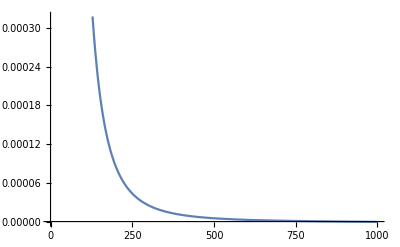

```mathematica
Plot[%66,{y,0.1,1000}]
```

```mathematica
Manipulate[Manipulate[Manipulate[Manipulate[Plot[{(m π y ArcTan[(2 R-y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(m π y ArcTan[(2 R+y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(π (-8 R y-(4 R^2+y^2-m y^2+4 μ) (Log[R^2-R y+1/4 (1+m) y^2+μ]-Log[R^2+R y+1/4 (1+m) y^2+μ])))/(4 y^2)},{y,0.1,5000}],{m,0.01,2}],{α,1,1000}],{μ,0.01,10}],{R,1,1000}]
```

```mathematica
Manipulate[Manipulate[Manipulate[Manipulate[Maximize[{(m π y ArcTan[(2 R-y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(m π y ArcTan[(2 R+y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(π (-8 R y-(4 R^2+y^2-m y^2+4 μ) (Log[R^2-R y+1/4 (1+m) y^2+μ]-Log[R^2+R y+1/4 (1+m) y^2+μ])))/(4 y^2)},y],{m,0.01,2}],{α,1,1000}],{μ,0.01,10}],{R,1,10000}]
```

```mathematica
Manipulate[Manipulate[Manipulate[Plot[{-(2 π)/y+(m π y ArcTan[(2-y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(m π y ArcTan[(2+y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))-(π ((-1+m) y^2-4 (1+μ)) (Log[1+y+1/4 (1+m) y^2+μ]-Log[1+1/4 y (-4+y+m y)+μ]))/(4 y^2)},{y,0.1,10}],{m,0.01,2}],{α,1,1000}],{μ,0.01,10}]
```

```mathematica
Manipulate[Manipulate[Manipulate[Maximize[{-(2 π)/y+(m π y ArcTan[(2-y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))+(m π y ArcTan[(2+y)/(√(m y^2+4 μ))])/(√(m y^2+4 μ))-(π ((-1+m) y^2-4 (1+μ)) (Log[1+y+1/4 (1+m) y^2+μ]-Log[1+1/4 y (-4+y+m y)+μ]))/(4 y^2)},y],{m,0.01,1}],{α,1,100}],{μ,0.1,10}]
```

```mathematica
Manipulate[Manipulate[Plot[{L[1,y,(1+m)y^2/4+μ],4 π √μ ArcTan[1/(√μ)]},{y,0,100}],{m,0.01,1}],{μ,0.1,10000}]
```

```mathematica
D[L[1,y,α],α]
```

(π (2/(1-y+α)-y^2/(1-y+α)+(2 α)/(1-y+α)-2/(1+y+α)+y^2/(1+y+α)-(2 α)/(1+y+α)-(4 (2-y) y)/((-y^2+4 α) (1+(2-y)^2/(-y^2+4 α)))-(4 y (2+y))/((-y^2+4 α) (1+(2+y)^2/(-y^2+4 α)))+(4 y ArcTan[(2-y)/(√(-y^2+4 α))])/(√(-y^2+4 α))+(4 y ArcTan[(2+y)/(√(-y^2+4 α))])/(√(-y^2+4 α))+2 Log[1-y+α]-2 Log[1+y+α]))/(2 y)

```mathematica
%//FullSimplify
```

(π (-2 y ArcTan[(-2+y)/(√(-y^2+4 α))]+2 y ArcTan[(2+y)/(√(-y^2+4 α))]+√(-y^2+4 α) (Log[1-y+α]-Log[1+y+α])))/(y √(-y^2+4 α))

```mathematica
Manipulate[Manipulate[Plot[{(π (-2 y ArcTan[(-2+y)/(√(-y^2+4 α))]+2 y ArcTan[(2+y)/(√(-y^2+4 α))]+√(-y^2+4 α) (Log[1-y+α]-Log[1+y+α])))/(y √(-y^2+4 α))},{α,(1+m)y^2/4,10(1+m)y^2/4}],{y,10,100}],{m,0.01,1}]
```

```mathematica
Limit[L[n,y,α],y->0]
```

4 π √α ArcTan[n/(√α)]

```mathematica
.bd
```

```mathematica
Manipulate[4Pi*Sqrt[μ]ArcTan[1/Sqrt[μ]],{μ,0.1,100}]
```

```mathematica
Solve[4Pi*(1-Sqrt[μ](3 1/Sqrt[μ])/(1+2Sqrt[1+(1/Sqrt[μ])^2]))==(4Pi-α)/N,μ]
```

{{μ→(4 (16 π^2-32 N π^2+16 N^2 π^2-8 π α+8 N π α+α^2))/(3 (4 π-α) (-4 π+16 N π+α))}}

```mathematica
Series[(4 (16 π^2-32 N π^2+16 N^2 π^2-8 π α+8 N π α+α^2))/(3 (4 π-α) (-4 π+16 N π+α)),{α,Infinity,5}]
```

-4/3+(32 N π)/(3 α)-(64 (-2 N π^2+9 N^2 π^2))/(3 α^2)+(512 (N π^3-9 N^2 π^3+18 N^3 π^3))/(3 α^3)-(1024 (-2 N π^4+27 N^2 π^4-108 N^3 π^4+144 N^4 π^4))/(3 α^4)+(8192 (N π^5-18 N^2 π^5+108 N^3 π^5-288 N^4 π^5+288 N^5 π^5))/(3 α^5)+O[1/α]^6

```mathematica
D[(4 (16 π^2-32 N π^2+16 N^2 π^2-8 π α+8 N π α+α^2))/(3 (4 π-α) (-4 π+16 N π+α)),α]
```

(4 (-8 π+8 N π+2 α))/(3 (4 π-α) (-4 π+16 N π+α))-(4 (16 π^2-32 N π^2+16 N^2 π^2-8 π α+8 N π α+α^2))/(3 (4 π-α) (-4 π+16 N π+α)^2)+(4 (16 π^2-32 N π^2+16 N^2 π^2-8 π α+8 N π α+α^2))/(3 (4 π-α)^2 (-4 π+16 N π+α))

```mathematica
%//FullSimplify
```

4/3 N π (1/(-4 π+α)^2-9/(4 (-1+4 N) π+α)^2)

```mathematica
Solve[%==0,α]
```

{{α→-4 (-π+N π)},{α→4 (π+2 N π)}}

```mathematica
Limit[]
```

```mathematica
(4 (16 π^2-32 N π^2+16 N^2 π^2-8 π α+8 N π α+α^2))/(3 (4 π-α) (-4 π+16 N π+α))//FullSimplify
```

(4 (4 (-1+N) π+α)^2)/(3 (4 π-α) (4 (-1+4 N) π+α))

```mathematica
Limit[L[n,2/(1+m)k,k^2+μ],k->0]
```

$Aborted

```mathematica
Integrate[x^2/(x^2+λ),{x,0,n}]
```

ConditionalExpression[n-√λ ArcTan[n/(√λ)],Re[(√λ)/n]≠0||Im[(√λ)/n]>1||Im[(√λ)/n]<-1]

```mathematica
NSolve[x*ArcTan[10/x]==4&&x>0,x]
```

{{x→3.16355}}

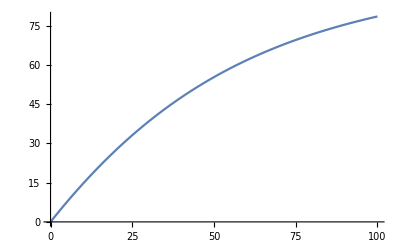

```mathematica
Plot[x*ArcTan[100/x],{x,0,100}]
```

```mathematica
Integrate[x^2/((x^2+λ)^2),{x,0,n}]
```

ConditionalExpression[1/2 (-n/(n^2+λ)+ArcTan[n/(√λ)]/(√λ)),Re[(√λ)/n]≠0||Im[(√λ)/n]>1||Im[(√λ)/n]<-1]

```mathematica
Integrate[k^4/(k^2+)]
```